# Bistable motif: detailed balancing and its consequences

## Finding the condition of multistationarity

We consider the following reactions:

K+S⇋KS→K+S_p
K^✶+S⇋K^✶S→K^✶+S_p
S_p→S
K⇋K^✶
KS⇋K^✶S

The species of the system are:

{S,S_p,K,K^✶,KS,K^✶S}

In total, there are 11 reations and 6 species.

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
ClearAll["Global`*"];
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms]
```

-k_2^2 k_5^2 k_7 k_8 k_9-2 k_2 k_3 k_5^2 k_7 k_8 k_9-k_3^2 k_5^2 k_7 k_8 k_9-2 k_2^2 k_5 k_6 k_7 k_8 k_9-4 k_2 k_3 k_5 k_6 k_7 k_8 k_9-2 k_3^2 k_5 k_6 k_7 k_8 k_9-k_2^2 k_6^2 k_7 k_8 k_9-2 k_2 k_3 k_6^2 k_7 k_8 k_9-k_3^2 k_6^2 k_7 k_8 k_9-k_2^2 k_5^2 k_7 k_9^2-2 k_2 k_3 k_5^2 k_7 k_9^2-k_3^2 k_5^2 k_7 k_9^2-2 k_2^2 k_5 k_6 k_7 k_9^2-4 k_2 k_3 k_5 k_6 k_7 k_9^2-2 k_3^2 k_5 k_6 k_7 k_9^2-k_2^2 k_6^2 k_7 k_9^2-2 k_2 k_3 k_6^2 k_7 k_9^2-k_3^2 k_6^2 k_7 k_9^2-2 k_2 k_5^2 k_7 k_8 k_9 k_10-2 k_3 k_5^2 k_7 k_8 k_9 k_10-4 k_2 k_5 k_6 k_7 k_8 k_9 k_10-4 k_3 k_5 k_6 k_7 k_8 k_9 k_10-2 k_2 k_6^2 k_7 k_8 k_9 k_10-2 k_3 k_6^2 k_7 k_8 k_9 k_10-2 k_2 k_5^2 k_7 k_9^2 k_10-2 k_3 k_5^2 k_7 k_9^2 k_10-4 k_2 k_5 k_6 k_7 k_9^2 k_10-4 k_3 k_5 k_6 k_7 k_9^2 k_10-2 k_2 k_6^2 k_7 k_9^2 k_10-2 k_3 k_6^2 k_7 k_9^2 k_10-k_5^2 k_7 k_8 k_9 k_10^2-2 k_5 k_6 k_7 k_8 k_9 k_10^2-k_6^2 k_7 k_8 k_9 k_10^2-k_5^2 k_7 k_9^2 k_10^2-2 k_5 k_6 k_7 k_9^2 k_10^2-k_6^2 k_7 k_9^2 k_10^2-2 k_2^2 k_5 k_7 k_8 k_9 k_11-4 k_2 k_3 k_5 k_7 k_8 k_9 k_11-2 k_3^2 k_5 k_7 k_8 k_9 k_11-2 k_2^2 k_6 k_7 k_8 k_9 k_11-4 k_2 k_3 k_6 k_7 k_8 k_9 k_11-2 k_3^2 k_6 k_7 k_8 k_9 k_11-2 k_2^2 k_5 k_7 k_9^2 k_11-4 k_2 k_3 k_5 k_7 k_9^2 k_11-2 k_3^2 k_5 k_7 k_9^2 k_11-2 k_2^2 k_6 k_7 k_9^2 k_11-4 k_2 k_3 k_6 k_7 k_9^2 k_11-2 k_3^2 k_6 k_7 k_9^2 k_11-2 k_2 k_5 k_7 k_8 k_9 k_10 k_11-2 k_3 k_5 k_7 k_8 k_9 k_10 k_11-2 k_2 k_6 k_7 k_8 k_9 k_10 k_11-2 k_3 k_6 k_7 k_8 k_9 k_10 k_11-2 k_2 k_5 k_7 k_9^2 k_10 k_11-2 k_3 k_5 k_7 k_9^2 k_10 k_11-2 k_2 k_6 k_7 k_9^2 k_10 k_11-2 k_3 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_7 k_8 k_9 k_11^2-2 k_2 k_3 k_7 k_8 k_9 k_11^2-k_3^2 k_7 k_8 k_9 k_11^2-k_2^2 k_7 k_9^2 k_11^2-2 k_2 k_3 k_7 k_9^2 k_11^2-k_3^2 k_7 k_9^2 k_11^2+(-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_1^3+(-k_2^2 k_4 k_5 k_6 k_8^2-2 k_2 k_3 k_4 k_5 k_6 k_8^2-k_3^2 k_4 k_5 k_6 k_8^2-k_2^2 k_4 k_6^2 k_8^2-2 k_2 k_3 k_4 k_6^2 k_8^2-k_3^2 k_4 k_6^2 k_8^2-k_2^2 k_4 k_5 k_7 k_8^2-2 k_2 k_3 k_4 k_5 k_7 k_8^2-k_3^2 k_4 k_5 k_7 k_8^2-k_2^2 k_4 k_6 k_7 k_8^2-2 k_2 k_3 k_4 k_6 k_7 k_8^2-k_3^2 k_4 k_6 k_7 k_8^2-k_1 k_2 k_3 k_5^2 k_8 k_9-k_1 k_3^2 k_5^2 k_8 k_9-2 k_1 k_2 k_3 k_5 k_6 k_8 k_9-2 k_1 k_3^2 k_5 k_6 k_8 k_9-k_2^2 k_4 k_5 k_6 k_8 k_9-2 k_2 k_3 k_4 k_5 k_6 k_8 k_9-k_3^2 k_4 k_5 k_6 k_8 k_9-k_1 k_2 k_3 k_6^2 k_8 k_9-k_1 k_3^2 k_6^2 k_8 k_9-k_2^2 k_4 k_6^2 k_8 k_9-2 k_2 k_3 k_4 k_6^2 k_8 k_9-k_3^2 k_4 k_6^2 k_8 k_9-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_8 k_9-k_1 k_3 k_5^2 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-2 k_1 k_2 k_5 k_6 k_7 k_8 k_9-2 k_1 k_3 k_5 k_6 k_7 k_8 k_9-k_1 k_2 k_6^2 k_7 k_8 k_9-k_1 k_3 k_6^2 k_7 k_8 k_9-k_1 k_2 k_3 k_5^2 k_9^2-k_1 k_3^2 k_5^2 k_9^2-2 k_1 k_2 k_3 k_5 k_6 k_9^2-2 k_1 k_3^2 k_5 k_6 k_9^2-k_1 k_2 k_3 k_6^2 k_9^2-k_1 k_3^2 k_6^2 k_9^2-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-2 k_2 k_4 k_5 k_6 k_8^2 k_10-2 k_3 k_4 k_5 k_6 k_8^2 k_10-2 k_2 k_4 k_6^2 k_8^2 k_10-2 k_3 k_4 k_6^2 k_8^2 k_10-2 k_2 k_4 k_5 k_7 k_8^2 k_10-2 k_3 k_4 k_5 k_7 k_8^2 k_10-2 k_2 k_4 k_6 k_7 k_8^2 k_10-2 k_3 k_4 k_6 k_7 k_8^2 k_10-k_1 k_3 k_5^2 k_8 k_9 k_10-k_1 k_2 k_5 k_6 k_8 k_9 k_10-3 k_1 k_3 k_5 k_6 k_8 k_9 k_10-2 k_2 k_4 k_5 k_6 k_8 k_9 k_10-2 k_3 k_4 k_5 k_6 k_8 k_9 k_10-k_1 k_2 k_6^2 k_8 k_9 k_10-2 k_1 k_3 k_6^2 k_8 k_9 k_10-2 k_2 k_4 k_6^2 k_8 k_9 k_10-2 k_3 k_4 k_6^2 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_8 k_9 k_10-k_1 k_3 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-k_1 k_5^2 k_7 k_8 k_9 k_10-k_1 k_2 k_6 k_7 k_8 k_9 k_10-k_1 k_3 k_6 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-2 k_1 k_5 k_6 k_7 k_8 k_9 k_10-k_1 k_6^2 k_7 k_8 k_9 k_10-k_1 k_3 k_5^2 k_9^2 k_10-k_1 k_2 k_5 k_6 k_9^2 k_10-3 k_1 k_3 k_5 k_6 k_9^2 k_10-k_1 k_2 k_6^2 k_9^2 k_10-2 k_1 k_3 k_6^2 k_9^2 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_4 k_5 k_6 k_8^2 k_10^2-k_4 k_6^2 k_8^2 k_10^2-k_4 k_5 k_7 k_8^2 k_10^2-k_4 k_6 k_7 k_8^2 k_10^2-k_1 k_5 k_6 k_8 k_9 k_10^2-k_4 k_5 k_6 k_8 k_9 k_10^2-k_1 k_6^2 k_8 k_9 k_10^2-k_4 k_6^2 k_8 k_9 k_10^2-k_1 k_5 k_7 k_8 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_1 k_6 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_6 k_9^2 k_10^2-k_1 k_6^2 k_9^2 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2 k_3 k_4 k_5 k_8^2 k_11-k_3^2 k_4 k_5 k_8^2 k_11-k_2^2 k_4 k_6 k_8^2 k_11-3 k_2 k_3 k_4 k_6 k_8^2 k_11-2 k_3^2 k_4 k_6 k_8^2 k_11-k_2^2 k_4 k_7 k_8^2 k_11-2 k_2 k_3 k_4 k_7 k_8^2 k_11-k_3^2 k_4 k_7 k_8^2 k_11-k_2 k_4 k_5 k_7 k_8^2 k_11-k_3 k_4 k_5 k_7 k_8^2 k_11-k_2 k_4 k_6 k_7 k_8^2 k_11-k_3 k_4 k_6 k_7 k_8^2 k_11-2 k_1 k_2 k_3 k_5 k_8 k_9 k_11-2 k_1 k_3^2 k_5 k_8 k_9 k_11-k_2 k_3 k_4 k_5 k_8 k_9 k_11-k_3^2 k_4 k_5 k_8 k_9 k_11-2 k_1 k_2 k_3 k_6 k_8 k_9 k_11-2 k_1 k_3^2 k_6 k_8 k_9 k_11-k_2^2 k_4 k_6 k_8 k_9 k_11-3 k_2 k_3 k_4 k_6 k_8 k_9 k_11-2 k_3^2 k_4 k_6 k_8 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_8 k_9 k_11-2 k_1 k_3 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-2 k_1 k_2 k_6 k_7 k_8 k_9 k_11-2 k_1 k_3 k_6 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_3 k_5 k_9^2 k_11-2 k_1 k_3^2 k_5 k_9^2 k_11-2 k_1 k_2 k_3 k_6 k_9^2 k_11-2 k_1 k_3^2 k_6 k_9^2 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_3 k_4 k_5 k_8^2 k_10 k_11-k_2 k_4 k_6 k_8^2 k_10 k_11-2 k_3 k_4 k_6 k_8^2 k_10 k_11-k_2 k_4 k_7 k_8^2 k_10 k_11-k_3 k_4 k_7 k_8^2 k_10 k_11-k_4 k_5 k_7 k_8^2 k_10 k_11-k_4 k_6 k_7 k_8^2 k_10 k_11-k_1 k_3 k_5 k_8 k_9 k_10 k_11-k_3 k_4 k_5 k_8 k_9 k_10 k_11-k_1 k_2 k_6 k_8 k_9 k_10 k_11-2 k_1 k_3 k_6 k_8 k_9 k_10 k_11-k_2 k_4 k_6 k_8 k_9 k_10 k_11-2 k_3 k_4 k_6 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_7 k_8 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_1 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_1 k_6 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_5 k_9^2 k_10 k_11-k_1 k_2 k_6 k_9^2 k_10 k_11-2 k_1 k_3 k_6 k_9^2 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2 k_3 k_4 k_8^2 k_11^2-k_3^2 k_4 k_8^2 k_11^2-k_2 k_4 k_7 k_8^2 k_11^2-k_3 k_4 k_7 k_8^2 k_11^2-k_1 k_2 k_3 k_8 k_9 k_11^2-k_1 k_3^2 k_8 k_9 k_11^2-k_2 k_3 k_4 k_8 k_9 k_11^2-k_3^2 k_4 k_8 k_9 k_11^2-k_1 k_2 k_7 k_8 k_9 k_11^2-k_1 k_3 k_7 k_8 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_3 k_9^2 k_11^2-k_1 k_3^2 k_9^2 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2) x_3+x_1^2 (-k_1 k_2 k_4 k_5 k_7 k_9 k_10-k_1 k_3 k_4 k_5 k_7 k_9 k_10-k_1 k_2 k_4 k_6 k_7 k_9 k_10-k_1 k_3 k_4 k_6 k_7 k_9 k_10-k_1 k_4 k_5 k_7 k_9 k_10^2-k_1 k_4 k_6 k_7 k_9 k_10^2-k_2^2 k_4^2 k_7 k_8 k_11-2 k_2 k_3 k_4^2 k_7 k_8 k_11-k_3^2 k_4^2 k_7 k_8 k_11-2 k_1 k_2 k_4 k_5 k_7 k_9 k_11-2 k_1 k_3 k_4 k_5 k_7 k_9 k_11-2 k_1 k_2 k_4 k_6 k_7 k_9 k_11-2 k_1 k_3 k_4 k_6 k_7 k_9 k_11-k_1 k_2 k_4 k_5 k_7 k_10 k_11-k_1 k_3 k_4 k_5 k_7 k_10 k_11-k_1 k_2 k_4 k_6 k_7 k_10 k_11-k_1 k_3 k_4 k_6 k_7 k_10 k_11-k_2 k_4^2 k_7 k_8 k_10 k_11-k_3 k_4^2 k_7 k_8 k_10 k_11-2 k_1 k_2 k_4 k_7 k_9 k_10 k_11-2 k_1 k_3 k_4 k_7 k_9 k_10 k_11-k_1 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_4 k_6 k_7 k_9 k_10 k_11-k_2^2 k_4^2 k_7 k_11^2-2 k_2 k_3 k_4^2 k_7 k_11^2-k_3^2 k_4^2 k_7 k_11^2-k_2 k_4^2 k_7 k_8 k_11^2-k_3 k_4^2 k_7 k_8 k_11^2-2 k_1 k_2 k_4 k_7 k_9 k_11^2-2 k_1 k_3 k_4 k_7 k_9 k_11^2+(k_1^2 k_3 k_4 k_5 k_9 k_10+k_1^2 k_3 k_4 k_6 k_9 k_10-k_1^2 k_4 k_5 k_6 k_9 k_10-k_1^2 k_4 k_6^2 k_9 k_10-k_1^2 k_4 k_5 k_6 k_10^2-k_1^2 k_4 k_6^2 k_10^2-k_1^2 k_4 k_5 k_7 k_10^2-k_1^2 k_4 k_6 k_7 k_10^2-k_1 k_2 k_3 k_4^2 k_8 k_11-k_1 k_3^2 k_4^2 k_8 k_11+k_1 k_2 k_4^2 k_6 k_8 k_11+k_1 k_3 k_4^2 k_6 k_8 k_11-k_1^2 k_3 k_4 k_5 k_10 k_11-k_1^2 k_3 k_4 k_6 k_10 k_11-k_1 k_2 k_4^2 k_6 k_10 k_11-k_1 k_3 k_4^2 k_6 k_10 k_11-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1^2 k_4 k_5 k_7 k_10 k_11-k_1^2 k_4 k_6 k_7 k_10 k_11-k_1 k_2 k_3 k_4^2 k_11^2-k_1 k_3^2 k_4^2 k_11^2-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_3)+x_1 (-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-k_1 k_2 k_5^2 k_7 k_9 k_10-k_1 k_3 k_5^2 k_7 k_9 k_10-2 k_1 k_2 k_5 k_6 k_7 k_9 k_10-2 k_1 k_3 k_5 k_6 k_7 k_9 k_10-k_1 k_2 k_6^2 k_7 k_9 k_10-k_1 k_3 k_6^2 k_7 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9 k_10^2-2 k_1 k_5 k_6 k_7 k_9 k_10^2-k_1 k_6^2 k_7 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2^2 k_4 k_5 k_7 k_8 k_11-2 k_2 k_3 k_4 k_5 k_7 k_8 k_11-k_3^2 k_4 k_5 k_7 k_8 k_11-k_2^2 k_4 k_6 k_7 k_8 k_11-2 k_2 k_3 k_4 k_6 k_7 k_8 k_11-k_3^2 k_4 k_6 k_7 k_8 k_11-2 k_2^2 k_4 k_5 k_7 k_9 k_11-4 k_2 k_3 k_4 k_5 k_7 k_9 k_11-2 k_3^2 k_4 k_5 k_7 k_9 k_11-2 k_2^2 k_4 k_6 k_7 k_9 k_11-4 k_2 k_3 k_4 k_6 k_7 k_9 k_11-2 k_3^2 k_4 k_6 k_7 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_2 k_4 k_5 k_7 k_8 k_10 k_11-k_3 k_4 k_5 k_7 k_8 k_10 k_11-k_2 k_4 k_6 k_7 k_8 k_10 k_11-k_3 k_4 k_6 k_7 k_8 k_10 k_11-k_1 k_2 k_5 k_7 k_9 k_10 k_11-k_1 k_3 k_5 k_7 k_9 k_10 k_11-2 k_2 k_4 k_5 k_7 k_9 k_10 k_11-2 k_3 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_2 k_6 k_7 k_9 k_10 k_11-k_1 k_3 k_6 k_7 k_9 k_10 k_11-2 k_2 k_4 k_6 k_7 k_9 k_10 k_11-2 k_3 k_4 k_6 k_7 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_4 k_7 k_8 k_11^2-2 k_2 k_3 k_4 k_7 k_8 k_11^2-k_3^2 k_4 k_7 k_8 k_11^2-2 k_2^2 k_4 k_7 k_9 k_11^2-4 k_2 k_3 k_4 k_7 k_9 k_11^2-2 k_3^2 k_4 k_7 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2-2 (k_1 k_2 k_4 k_5 k_6 k_8 k_10+k_1 k_3 k_4 k_5 k_6 k_8 k_10+k_1 k_2 k_4 k_6^2 k_8 k_10+k_1 k_3 k_4 k_6^2 k_8 k_10+k_1 k_2 k_4 k_5 k_7 k_8 k_10+k_1 k_3 k_4 k_5 k_7 k_8 k_10+k_1 k_2 k_4 k_6 k_7 k_8 k_10+k_1 k_3 k_4 k_6 k_7 k_8 k_10+k_1 k_2 k_4 k_5 k_6 k_9 k_10+k_1 k_3 k_4 k_5 k_6 k_9 k_10+k_1 k_2 k_4 k_6^2 k_9 k_10+k_1 k_3 k_4 k_6^2 k_9 k_10+k_1 k_2 k_4 k_5 k_7 k_9 k_10+k_1 k_3 k_4 k_5 k_7 k_9 k_10+k_1 k_2 k_4 k_6 k_7 k_9 k_10+k_1 k_3 k_4 k_6 k_7 k_9 k_10+k_1 k_4 k_5 k_6 k_8 k_10^2+k_1 k_4 k_6^2 k_8 k_10^2+k_1 k_4 k_5 k_7 k_8 k_10^2+k_1 k_4 k_6 k_7 k_8 k_10^2+k_1 k_4 k_5 k_6 k_9 k_10^2+k_1 k_4 k_6^2 k_9 k_10^2+k_1 k_4 k_5 k_7 k_9 k_10^2+k_1 k_4 k_6 k_7 k_9 k_10^2+k_1 k_2 k_3 k_4 k_5 k_8 k_11+k_1 k_3^2 k_4 k_5 k_8 k_11+k_1 k_2 k_3 k_4 k_6 k_8 k_11+k_1 k_3^2 k_4 k_6 k_8 k_11+k_1 k_2 k_4 k_5 k_7 k_8 k_11+k_1 k_3 k_4 k_5 k_7 k_8 k_11+k_1 k_2 k_4 k_6 k_7 k_8 k_11+k_1 k_3 k_4 k_6 k_7 k_8 k_11+k_1 k_2 k_3 k_4 k_5 k_9 k_11+k_1 k_3^2 k_4 k_5 k_9 k_11+k_1 k_2 k_3 k_4 k_6 k_9 k_11+k_1 k_3^2 k_4 k_6 k_9 k_11+k_1 k_2 k_4 k_5 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_7 k_9 k_11+k_1 k_2 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_8 k_10 k_11+k_1 k_2 k_4 k_6 k_8 k_10 k_11+2 k_1 k_3 k_4 k_6 k_8 k_10 k_11+k_1 k_2 k_4 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_7 k_8 k_10 k_11+k_1 k_4 k_5 k_7 k_8 k_10 k_11+k_1 k_4 k_6 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_5 k_9 k_10 k_11+k_1 k_2 k_4 k_6 k_9 k_10 k_11+2 k_1 k_3 k_4 k_6 k_9 k_10 k_11+k_1 k_2 k_4 k_7 k_9 k_10 k_11+k_1 k_3 k_4 k_7 k_9 k_10 k_11+k_1 k_4 k_5 k_7 k_9 k_10 k_11+k_1 k_4 k_6 k_7 k_9 k_10 k_11+k_1 k_2 k_3 k_4 k_8 k_11^2+k_1 k_3^2 k_4 k_8 k_11^2+k_1 k_2 k_4 k_7 k_8 k_11^2+k_1 k_3 k_4 k_7 k_8 k_11^2+k_1 k_2 k_3 k_4 k_9 k_11^2+k_1 k_3^2 k_4 k_9 k_11^2+k_1 k_2 k_4 k_7 k_9 k_11^2+k_1 k_3 k_4 k_7 k_9 k_11^2) x_3)

```mathematica
factor=Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
Factor[factor]
```

k_1 k_4 (k_1 k_3 k_5 k_9 k_10+k_1 k_3 k_6 k_9 k_10-k_1 k_5 k_6 k_9 k_10-k_1 k_6^2 k_9 k_10-k_1 k_5 k_6 k_10^2-k_1 k_6^2 k_10^2-k_1 k_5 k_7 k_10^2-k_1 k_6 k_7 k_10^2-k_2 k_3 k_4 k_8 k_11-k_3^2 k_4 k_8 k_11+k_2 k_4 k_6 k_8 k_11+k_3 k_4 k_6 k_8 k_11-k_1 k_3 k_5 k_10 k_11-k_1 k_3 k_6 k_10 k_11-k_2 k_4 k_6 k_10 k_11-k_3 k_4 k_6 k_10 k_11-k_2 k_4 k_7 k_10 k_11-k_3 k_4 k_7 k_10 k_11-k_1 k_5 k_7 k_10 k_11-k_1 k_6 k_7 k_10 k_11-k_2 k_3 k_4 k_11^2-k_3^2 k_4 k_11^2-k_2 k_4 k_7 k_11^2-k_3 k_4 k_7 k_11^2)

```mathematica
term=Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
simpTerm=FullSimplify[term]
```

-(k_2+k_3) k_4 k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11))-k_1 (k_5+k_6) k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11))

```mathematica
simplerTerm=Distribute[simpTerm/(Subscript[k, 1]*Subscript[k, 4])]/.{(Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1]-> Subscript[M, 1],(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]-> Subscript[M, 2]}
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2

This above term larger than 0 should be the necessary condition.

```mathematica
condition=simplerTerm>0
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2>0

By mannual simplying the term, we can have:

```mathematica
simpleCond=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])>(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))
```

(k_3-k_6) (-k_8 k_11 M_1+k_9 k_10 M_2)>(k_6 k_10+k_3 k_11+k_7 (k_10+k_11)) (k_11 M_1+k_10 M_2)

```mathematica
left=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)

```mathematica
right=(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

To fullfile the assumption of thermodynamic conditions for the reversible reactions, we have the the constraint:
(k_1 k_10)/(k_2 k_11)=(k_4 k_8)/(k_5 k_9).
This will give us a even simple condition. Then we will example how will this condition result in the parameter space for multistationarity.

```mathematica
oriCond=simpleCond/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

```mathematica
Simplify[oriCond,Assumptions->(Subscript[k, 1] Subscript[k, 10])/(Subscript[k, 2] Subscript[k, 11])==(Subscript[k, 4] Subscript[k, 8])/(Subscript[k, 5] Subscript[k, 9])]
```

((k_3-k_6) (k_1 k_6 k_9 k_10-k_3 k_4 k_8 k_11))/(k_1 k_4)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Better to do it manually, then we have the condition with thermodynamic constraint:

```mathematica
thermoCond=(Subscript[k, 3]-Subscript[k, 6])(Subscript[k, 6] Subscript[k, 2]-Subscript[k, 3] Subscript[k, 5])>(Subscript[k, 2]/Subscript[k, 9]×(Subscript[k, 5]^2 +Subscript[k, 6])/Subscript[k, 5]+Subscript[k, 5]/Subscript[k, 8]×(Subscript[k, 2]^2+Subscript[k, 3])/Subscript[k, 2])((Subscript[k, 6]+Subscript[k, 7]) Subscript[k, 10]+(Subscript[k, 3]+Subscript[k, 7]) Subscript[k, 11])
```

(k_3-k_6) (-k_3 k_5+k_2 k_6)>(((k_2^2+k_3) k_5)/(k_2 k_8)+(k_2 (k_5^2+k_6))/(k_5 k_9)) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Fromt the above condition, we can get some general idea that in order to satisfy the thermodynamic condition we should have:
Necessarily:
k_3>k_6 and k_2>k_5
or
k_3<k_6 and k_5>k_2
With additional:
k_8,k_9≫k_10,k_11 and k_7,k_10,k_11≈0

## Sampling the parameters (without thermodynamic constraint)

Here we try to sampling the parameters by enforcing the thermodynamc constraint. The parameters are sampled in biologically meaningful ranges.

```mathematica
ClearAll["Global`*"];
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms];
(*The above code is the same as first section*)

bistableKs={};
bistableParSets={};
SeedRandom[];
Timing[
Do[{
rands=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],11]]*1000;
k1=rands[[1]];k2=rands[[2]];k3=rands[[3]];k4=rands[[4]];k5=rands[[5]];k6=rands[[6]];k7=rands[[7]];k8=rands[[8]];k9=rands[[9]];k10=rands[[10]];k11=rands[[11]];
left=(k3-k6) (((k5+k6) k9 k10)/k4-((k2+k3) k8 k11)/k1);right=(((k5+k6) k10)/k4+((k2+k3) k11)/k1) (k6 k10+k3 k11+k7 (k10+k11));If[left>right,{
AppendTo[bistableKs,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,left,right}];
counter=1;hitQ=0;
While[hitQ==0&&counter≤1000,{
x1=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.0001])]]]*1000;
finalSol=NSolve[finalSubs==0/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1},{Subscript[x, 3]}];
x3=Subscript[x, 3]/.finalSol[[1]];
realSol=solution/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1,Subscript[x, 3]->x3};
T1=(Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
T2=(Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
If[0.0001≤T1≤1000&&0.0001≤T2≤1000,{
AppendTo[bistableParSets,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,T1,T2,left,right}];
hitQ=1;
}];
counter++;
}];
}];
},{i,10000}];
]
```

{8863.5,Null}

```mathematica
Length[bistableParSets]
```

185

```mathematica
InputForm[bistableParSets]
```

{{409.00927432243276, 76.71652092309492, 1.404628225921411, 73.88194900935866, 27.6267964199818, 0.004701922250428076, 
  0.5395996447972011, 1.3914029766005262*^-11, 67.28154225753546, 22.76352126408187, 1.074396743675682*^-7, 18.79798279270573, 
  10.989502844017279, 801.8749508326912, 105.48350980597111}, {0.00035317889372508, 0.03289302301484053, 3.118854206251663*^-8, 
  14.431008470168791, 7.254182647383911*^-6, 947.9075511528705, 6.844460169426479*^-6, 0.005784943829521705, 
  7.128722417501903*^-20, 1.0131725721706671*^-11, 6.129945671535569, 139.11626972184845, 0.001274933071784338, 
  3130.626186434406, 0.02406774154405327}, {66.12141243225254, 77.93422833025461, 10.6287427194999, 17.259907015283098, 
  16.856372553500016, 0.041047575135374145, 0.0038661799752154015, 1.9512663582811397*^-22, 59.10775909435813, 
  1.6665412639250528, 4.0987056209200445*^-6, 402.0622831949163, 0.4990677804697607, 1021.0427937455011, 0.12219338758680857}, 
 {17.73555358875413, 0.30918084846747085, 6.0288802472169305, 32.30436096817457, 71.8484962262466, 0.49792768774858476, 
  0.00006614846777475584, 3.1294115902657174*^-10, 95.20523698142536, 174.82891181164825, 3.1718925103955007*^-10, 
  147.13825682799288, 0.012129642172470772, 206172.1218672796, 34088.382204987895}, 
 {21.184585282311343, 13.180551616371174, 0.062012744206406734, 97.60864520900772, 53.4768773576975, 21.929304268507554, 
  0.021802899151739566, 0.8419063900930455, 378.01529751695364, 2.047730920271936*^-10, 19.06859228132801, 693.2783252273072, 
  153.90431594357725, 219.4469538568205, 19.050855187804494}, {48.400748033843996, 3.452075736872739*^-8, 117.50750495276945, 
  71.00672160383039, 1.6024917728183001, 474.1934494660622, 0.14517275451530368, 509.837508372637, 8.67239447007212*^-6, 
  0.006249457484262956, 328.38262057882395, 710.7071885709439, 0.7278990527357774, 1.4498112810081443*^8, 3.080575149577571*^7}, 
 {867.8930411530439, 3.1164661458351305*^-6, 1.7167703580994368*^-13, 4.099432962550786, 1.956628779937843*^-9, 
  0.10701657164555926, 3.32599445022641*^-11, 10.853414342921653, 0.0034423593136992813, 2.8797037209057125*^-6, 
  34.47878654793829, 53.54326646360742, 0.19234751797792413, 1.4377453627212245*^-7, 6.155119549319149*^-14}, 
 {134.0302577893335, 4.145932672703278, 0.0343276214061556, 4.140207306494101, 6.288926022692458*^-7, 11.212235206980475, 
  0.04145734956986996, 761.4320082661737, 0.000011619017394496876, 0.007150626601549602, 0.6498098442857079, 135.51283544529537, 
  0.7757829555029526, 172.49574877438062, 0.005140899888881114}, {14.693734684639978, 313.7731554708713, 2.0479113788857347*^-7, 
  26.030483959763608, 0.13513147044652782, 775.7731112372555, 3.259884554407347, 45.481257016569266, 0.17364992938376111, 
  3.0055039356545494, 444.8266469925824, 131.25470229846908, 10.082599872870603, 3.3513974126772636*^8, 3.635455327666984*^7}, 
 {109.15935591772553, 10.113904001852214, 0.2558479208532878, 14.632319384206768, 43.13466392749047, 2.3093729049880597*^-10, 
  9.208341878267947*^-11, 33.57316417062164, 7.192773490700568, 226.91874562849793, 0.30736446237011805, 863.787529757258, 
  0.00013392135908559243, 1230.7600901845103, 52.60639320953694}, {183.1393266073445, 0.000024047572745035744, 
  0.020200657559823965, 259.1295318754297, 4.776749307417024*^-10, 16.760193002489196, 0.00011398182393717976, 
  110.54420380523642, 0.5079310817140441, 0.4580863545836536, 15.882789533298844, 822.715393320303, 0.18976968214134693, 
  2.993852418184983, 0.2510698923920103}, {11.007935629601237, 6.841692067986194, 142.08013811471983, 37.13115804559668, 
  8.98447644322584*^-7, 0.337598037505671, 3.113559096216421, 0.026978744419141533, 193.43111056789354, 65.06561747366892, 
  4.64511270609655*^-7, 182.77686044903615, 146.4117285916392, 16219.61967256115, 132.84192595889436}, 
 {868.6279303042214, 0.000957434311696999, 632.1908688409902, 6.353794188263763, 0.00014464126671686126, 2.8631121288999566, 
  8.071578353855766*^-6, 2.5434456516000643, 2.8958522267976217, 450.56434623512473, 1.0249608371555384*^-10, 401.0866723963622, 
  0.0010857083695131648, 370030.27535297186, 261927.0666199766}, {0.22668210022757865, 7.358766629607327, 
  0.000021954349279998082, 653.724044139839, 2.345650783104755*^-8, 0.0010873293204724018, 2.9657344426063797*^-9, 
  6.923077343538551, 3.093921563935125*^-7, 1.306207007640391, 1.8030557758317922, 385.60606720963875, 0.0015025546839508952, 
  0.4317177776856565, 0.08545015426193076}, {641.3375869944766, 0.1587213309808361, 127.45646843419017, 76.30358523205243, 
  0.001686815165408044, 702.1878564411875, 0.04066053180958291, 792.5573263373676, 2.094762862124209*^-6, 1.3261904058265697, 
  67.75102629464764, 337.5252339561816, 0.07354664307386351, 6.140831140630127*^6, 245795.08410222235}, 
 {0.06876850823674246, 6.722824302190156, 126.49068742395733, 1.2769831213328684, 0.0009932513466312687, 7.184729173164713*^-7, 
  0.0002861033677329282, 7.577971236298672*^-7, 2.6095857693893456, 3.3145292442325895, 0.00019470862166683995, 
  70.10362481052873, 1.3033374022574011, 0.8515724132987872, 0.009713986523870316}, 
 {281.14403178783715, 7.666215844156038, 16.63000410524163, 38.66116575843331, 73.44000993706327, 4.568312271204361*^-8, 
  0.5440357452998031, 2.950543298223133*^-12, 348.1853479717683, 194.72764221338224, 0.00023145267647045666, 78.03329061423842, 
  14.801689522661528, 2.141845963359473*^6, 39188.332410819174}, {35.39306822217488, 1.9031848084549305*^-11, 643.11201280057, 
  136.74922883949336, 195.94958292821067, 1.8515245216422478, 0.00045269522026597584, 3.624790898737723, 31.20994273884053, 
  126.2568049226056, 9.958405033699253*^-8, 24.995217356724147, 0.0003682057411383058, 3.654989051840157*^6, 42702.09529380489}, 
 {69.02290540466086, 0.2840818437106677, 1.1362396018290138*^-6, 135.44906571737877, 0.13335514344094038, 23.483136723420138, 
  0.000011906240708834517, 4.189430602575675*^-6, 5.680069722864245*^-15, 7.401182254691488*^-11, 2.852556357319023*^-7, 
  103.4401707740839, 0.018538605815651064, 1.1550407289422582*^-13, 2.0673774411216554*^-18}, 
 {0.11094919088547073, 3.0609759372305536, 0.00023341700684433898, 218.45421700910038, 0.02041817267567665, 279.4216567749198, 
  0.00022911535107802267, 31.07892062213271, 2.3872245812950427*^-6, 9.911698536851275*^-9, 101.04003151583052, 
  702.3722598189026, 0.025060990583665937, 2.420962114138907*^7, 130.2937834193767}, 
 {3.90247017015633, 0.04836685420769162, 1.5199014268833945*^-6, 69.42589591830885, 37.01916198878908, 185.84337573236428, 
  0.10454131537767522, 0.028155591176185563, 0.004328074538025644, 4.760480195866822*^-21, 2.5434178179234967, 
  263.59294283373055, 248.44857922617894, 0.16494962738730684, 0.008382075917978115}, 
 {27.176964749117726, 6.578163816660122*^-6, 0.00006803530881780951, 184.14285785763136, 0.029104991173882926, 
  0.49062006935032443, 1.5325049357645792*^-9, 23.296943784522828, 2.430039192636327, 0.00034662413450377863, 
  172.96148043908568, 387.7902977885768, 0.008585033603255436, 0.0054257076710939565, 5.680470465864971*^-6}, 
 {33.173380918754, 8.045583721642377, 0.001943917134354927, 7.616772055250314, 315.77182733243893, 68.54118849131343, 
  0.0014712131796421172, 59.05235171514741, 7.716579228271507, 0.0005949245860669709, 191.5458641025342, 20.69192208564997, 
  0.05110580523069249, 188055.20966944576, 32.312322029795226}, {269.71950091257065, 0.027506225058826186, 
  5.884152264446506*^-6, 322.3157564870971, 281.9749272527453, 18.972857542792912, 4.846590914665384*^-8, 85.82530808549144, 
  0.00009004535202673796, 1.445328830743478*^-11, 4.848522374701039, 22.120083486348708, 0.00017776389884362765, 
  0.8053208174985177, 1.4225937538468651*^-8}, {731.6974266110146, 0.018615978606565633, 668.2410886312446, 4.966471493879244, 
  5.380419669379167*^-7, 0.7781508469623025, 9.932341755263899, 8.965062009951083*^-14, 22.259936579398893, 154.11280328369813, 
  0.012582314639731394, 273.6719668549931, 224.68654898809226, 358761.59506136767, 40081.963947654855}, 
 {109.14394876265104, 98.1452311086536, 212.00878698630095, 0.26509946202995843, 1.3633452966357997, 0.017764197507826682, 
  0.003503870610167735, 1.5066311162819073, 4.180674423274101, 959.048957052608, 0.0003317723529712092, 736.9687672997454, 
  44.34032986176665, 4.428165355807841*^6, 102264.29748096887}, {0.4261378797888825, 0.00039446453470998026, 
  4.058807408128932*^-12, 787.6956604607614, 2.7635793556430067*^-6, 2.784966721918008, 0.0010953483824924174, 
  159.8623882353095, 0.013634411691837949, 0.00001521752223238618, 0.1343824995440944, 864.9597005753006, 108.3853016922302, 
  0.05538177008271316, 2.3594444645879294*^-8}, {736.825893658861, 0.0004006904597150616, 0.27835859749310754, 
  416.0476067012836, 5.005226894655277*^-16, 41.097391895420145, 1.7506391959438343, 0.17078413922656138, 3.522270487371141*^-6, 
  8.051880963949998*^-7, 0.05246841210512898, 0.20508739615701502, 0.09662727334476032, 0.00013837976939636492, 
  2.1223611839041396*^-6}, {42.38206480306804, 0.015367848147836045, 0.24728526182191954, 233.82821218680633, 39.10732950819769, 
  5.7138675325553745*^-11, 5.707724006016632*^-7, 0.035251321451516666, 351.7378491137507, 476.97386336618, 
  0.004694005732575706, 63.002909748298194, 0.019610724387797502, 6938.621059337121, 0.11431727028417511}, 
 {0.9994978537389979, 37.49267945990883, 1.757216904391413*^-8, 143.1948064169567, 6.872753174844092, 197.36543522179602, 
  0.00007042283663297447, 17.983692085653708, 87.52522340963769, 0.015344101702356776, 111.33900154201154, 128.77705729812928, 
  0.0005582927984031526, 1.4823501927905183*^7, 12680.903219901125}, {439.0926796986788, 350.02661198510197, 
  1.172523769918234*^-11, 0.00004925151184425664, 0.00021265996040653322, 9.767645599839654*^-6, 3.6450280773404323*^-9, 
  0.02311595621735273, 5.638762439528859*^-8, 0.000010976810281956162, 0.6966850419652586, 229.7099755305507, 85.22330530486961, 
  1.2539568412236258*^-7, 1.474559233049567*^-9}, {0.2300346185130275, 0.00008277817155698217, 0.000282578350061176, 
  4.829152271513581, 0.8162769851782923, 2.775117638106417, 0.000827327599751557, 10.634793967366857, 1.6818030555989514, 
  0.0018002869751258695, 1.7317415656390756, 875.2814681261211, 162.2509555738248, 0.07491771054511626, 
  0.000028296363460012865}, {37.33045676581792, 0.03818165044499378, 1.1260384500083604, 953.2237176115685, 
  0.013192239073288313, 2.46838156137819, 0.00012204382582163785, 122.17350312194272, 162.47674843093822, 0.013475551869712808, 
  1.9365702539218677, 59.81877081814227, 0.004864561790795068, 9.897146460496792, 0.13380271850152273}, 
 {312.17455527039544, 98.86011042993405, 3.1070646712810787*^-6, 6.6326123032122695, 1.4076440457003323, 27.671073497885168, 
  0.029389477351840703, 3.6647573388463437, 5.907339201042218*^-13, 0.00021890489678939864, 706.1767772355611, 
  115.74771338176984, 94.63105766782765, 22678.180998629345, 4643.195402134592}, 
 {135.77783619127564, 131.43303226754145, 64.70077542855012, 362.15222429325456, 1.7698622043640002, 845.533254831011, 
  0.0000288740858150016, 246.43976010250066, 1.4783824231754319*^-18, 0.00013939772123679894, 8.549343974875969, 
  932.5542914344721, 0.00011529655532673139, 2.3764299356980575*^6, 6832.864940393768}, 
 {53.65658487610562, 0.00020032088327795212, 2.6220859347027616, 69.78393471621361, 0.0001855802873551072, 0.012490481485165319, 
  0.25925808290943486, 5.775127188383511*^-7, 0.9816987003622994, 0.021488992942377143, 0.004140848707496114, 5.273424248729686, 
  1.8077219876866726, 9.999611200132572*^-6, 3.6656487534281966*^-6}, {0.014145102474869903, 1.3016816694539608, 
  0.04715504236277521, 270.34513758161387, 8.753158815809233, 9.953892758870387, 0.00357252356823237, 2.6808144258870303, 
  29.23202762361045, 5.222524465846696*^-6, 73.69120051557617, 639.8941078947662, 15.306169290115577, 186623.4991768895, 
  26268.45975780485}, {71.99752659408114, 234.9128414762277, 396.0426925358531, 14.24716998407783, 6.845674517659323, 
  0.5118518682465907, 87.60306597263282, 4.839569203717223*^-10, 189.28389852162738, 0.6028424063531146, 0.0005137130361170526, 
  629.1408079895382, 151.96473391353373, 23307.787051888816, 16.85474337700532}, 
 {238.89819974244344, 113.68713902358918, 0.3521285189670601, 0.008992266727110601, 0.6559958761192436, 9.11476103043737*^-6, 
  1.3396750529215759*^-6, 0.00004045873568753525, 0.43161200376635245, 62.89367547971784, 0.026381619448121913, 
  251.22638952373907, 0.2410622723761517, 697.3140428903345, 45.640480115008174}, 
 {29.41968903939112, 9.910640443793188, 1.0578625372027843, 26.693699138057504, 23.546277748034527, 284.4318612859324, 
  1.2731312223501476, 204.26770709591764, 0.18243101758226463, 3.083963707340179*^-17, 325.7479991800529, 268.4015881415505, 
  80.61686838471186, 7.029925928747976*^6, 92217.61886079489}, {31.905248992063083, 0.010619743895937235, 176.94744186184138, 
  97.45059981615726, 2.2399252345483163*^-10, 31.04918995794426, 10.314837232769513, 0.3499650660520108, 10.205749334411477, 
  2.6585115533781467, 7.205688535123606*^-6, 111.7807300556569, 20.294123556290803, 1261.2424887548357, 93.15185254572607}, 
 {399.6331364552876, 26.553078325491313, 0.00010020082155854968, 627.9088399065162, 0.14309074961974066, 3.5833462134914065, 
  23.879474696148698, 16.3182314358717, 41.11031136556702, 4.0832512555060285*^-17, 0.02791087108088377, 774.4597077505448, 
  696.2166864032832, 0.108437158608324, 0.0012360282493082153}, {123.57205720101945, 54.59210686998486, 9.743713004327882, 
  0.37114351617555813, 0.4840534178330053, 1.9070214779549776*^-7, 2.6932891723375565*^-11, 1.0342651579845708*^-7, 
  0.5660952235789194, 334.15773206794427, 0.0002577906309790225, 771.845077481045, 0.00016551970612034808, 2403.903692158491, 
  1.122475438744927}, {189.55126431405665, 0.2659708869285546, 0.05858697410230702, 254.6666746112034, 482.0473768896711, 
  235.99681925926018, 0.0042800497230296285, 405.1509341894349, 12.256572412332318, 5.066920205516848*^-10, 19.416153849607653, 
  375.2827390802185, 8.355275132305628, 3177.9262687571745, 0.04058025935859232}, 
 {16.65514278187423, 729.8335871433793, 4.707302259130858*^-14, 23.54440644414485, 38.59589021504621, 13.9131365821127, 
  0.037295693972017, 15.063315632694822, 396.05824129998115, 0.00005832934746917196, 596.8740854277357, 684.3457890626034, 
  170.2411416281183, 5.481555014078567*^6, 582258.0508684956}, {152.66165279701752, 636.6201364268031, 1.8058677027614734*^-7, 
  870.398914375381, 4.304306208370305*^-6, 219.6291845925375, 0.00011053968378669074, 0.1766277096900133, 0.1638763652338222, 
  0.10009739462665554, 67.22213553365346, 40.290569131771825, 0.00887017574231919, 10873.6486483349, 6165.409021543172}, 
 {662.4166499662823, 1.1976053161452709, 0.6436715726255324, 53.979607579598664, 0.2071087019321799, 7.23367061381507*^-6, 
  0.274079139836515, 5.397700792161545, 3.296008200502918, 0.07440620476527578, 0.00006549692940510116, 1.9707699910160283, 
  1.1091144328186398, 0.0006050439111987589, 5.843117100529851*^-6}, {676.7162414566143, 5.484312815351107*^-19, 
  1.0133389525641658, 18.709387547356204, 56.061492439585706, 462.32568812551455, 36.34842617486795, 134.0945426355738, 
  0.0000634141964623356, 2.889373735675168*^-6, 0.00658595785860755, 630.7537488419779, 162.16744536883706, 0.6100586672182692, 
  0.000022255270437857915}, {0.17572475859857822, 0.00019936132306492695, 27.8588397665284, 4.150098249051843, 
  104.63706873152717, 0.05829960452085644, 0.004286364863351758, 2.651775716595224*^-7, 0.01112399056213918, 
  0.030181557212546742, 0.00003187521729854952, 282.0549844053868, 0.42932351482400466, 0.2354639968240148, 
  0.0021284960810299485}, {16.640877251767847, 5.225083736979939, 23.672379271165035, 264.47910361974914, 354.20686632782963, 
  0.1625233125802451, 3.8051399483387165, 0.00012912621659085145, 10.100547534998281, 19.710544254094952, 
  1.0909399356182395*^-11, 88.48929668065753, 62.41444078697444, 6271.31099050118, 2065.3652942802705}, 
 {537.031179455315, 0.000026726898254342494, 1.5934420011106432, 185.39431111504288, 1.950779038346306*^-19, 
  0.0006214247632278218, 0.0025972688695649815, 0.13407633985952125, 582.668009512747, 0.021754983394089142, 
  6.552612302400863*^-15, 4.407956071730662, 0.2456659737245943, 0.00006767666355336511, 5.106099874632067*^-12}, 
 {216.865735627218, 0.0007325874816639017, 444.8415645932877, 689.0765200098824, 279.2441895013081, 0.011526356744089682, 
  0.003285870740757004, 350.04254393883383, 0.16483316308803792, 42.47463197625732, 9.154112133918338*^-38, 503.1460809324789, 
  64.21827745124304, 1262.1266671877395, 10.829645530630325}, {481.62298076346156, 0.43791060115393143, 0.044586873531341914, 
  180.4466354663869, 0.005857215601529281, 116.55020091580838, 0.0014302599317376848, 3.81329226577689, 2.142003674027588*^-6, 
  1.1960338384059787*^-6, 5.996838330455484, 4.701564162432146, 0.04817015289199311, 2.6690525833339804, 0.0016589269362942316}, 
 {480.7713309702865, 0.000013050978732881514, 0.5779140752517146, 13.200156072615611, 0.022284501834019255, 
  3.2103938021559305*^-14, 0.13665454345291123, 0.0006269106599983954, 427.8874408959272, 0.03208062201336893, 
  0.02424766332431366, 286.4850312636739, 81.95301201611073, 0.0133924216131514, 1.8086263092159353*^-6}, 
 {907.3317269946624, 5.3094839157048193*^-14, 0.02163121053255785, 2.6304585816587345, 0.042524438488485465, 0.4238608562381748, 
  0.12644111563328178, 30.783397824859822, 0.0001936217362788358, 0.00008387881087069202, 0.35530136504340976, 
  317.6868843866978, 268.99433016569895, 0.00010488114944158878, 1.2291292748364805*^-6}, 
 {525.9821691510551, 0.14309037600869365, 0.00336011120968155, 2.883314288261981, 302.3723765986723, 0.0001643124032920227, 
  0.00013946349499208765, 0.06710305367241248, 11.123358502578213, 3.5449604432442916, 0.007008971146737252, 694.841020125254, 
  36.92992258818954, 13.215302953950486, 0.40945634600471764}, {5.0647184831366046, 1.652270058971521*^-6, 75.58515697819715, 
  148.24222031172556, 0.00800899121520298, 0.000016765510364532926, 0.03155944190907618, 1.6074071940742263, 55.45043416854844, 
  0.9316373037356391, 3.727274388936237*^-10, 426.39611256678603, 348.88985270251675, 0.21139802995763604, 
  1.48393915863345*^-6}, {8.062597356070196, 1.6273759707000442*^-7, 0.018391569284945997, 82.53405558269436, 
  0.028254246795063425, 0.000025329124295268953, 0.003074422331039006, 21.41463963528988, 1.0238405979946472, 
  0.027288270578420176, 1.8529558978186991*^-6, 506.49311975708144, 494.50054690470944, 1.741575881984743*^-7, 
  7.916241945838986*^-10}, {68.3113575600448, 214.0238637859133, 2.225541946051899*^-14, 82.78958972555003, 
  0.00008925353830126708, 0.6821467742810796, 0.0006603167223295846, 173.33222313531655, 0.007869440144078775, 
  0.00010481664462892136, 95.49133902739173, 259.85374046357794, 3.062538057902045, 35374.50767309231, 18.886096766887164}, 
 {429.1226050541557, 10.5697920210619, 109.16522342124767, 1.7172088922628619, 0.04319040382749848, 2.132989568099744, 
  1.3961832684738595, 981.7500224334071, 5.167731354618506, 33.023059058033624, 0.06580682396815518, 783.2094998923192, 
  261.17680413364286, 21218.050857340502, 5184.053914835916}, {289.10143615146234, 0.0004948784412113666, 511.8294483255061, 
  328.1730214642004, 1.6287332528272667*^-12, 7.805163747851285, 37.31719139587893, 0.10388931510896728, 359.44172935432573, 
  10.438662993503268, 0.000048259690089927266, 757.0612203682563, 504.45878557261324, 44978.392891345386, 116.98617022131248}, 
 {496.40943762949445, 116.12155446596059, 459.29090123560877, 27.944839125332436, 33.127924652680136, 1.8835858815771195*^-6, 
  339.8361018372797, 4.065216351702312, 24.726499439427403, 0.6853729370543474, 0.005454579318783384, 983.887724141909, 
  649.8938901875661, 9215.397715937193, 194.28313761550376}, {620.5092811611537, 0.000023502304389380224, 78.41746890207529, 
  2.5341047248769826, 165.84096928764498, 1.1443917269654114*^-13, 0.22675558157472972, 6.320611464826061, 119.62054919215537, 
  31.044279811529456, 5.2054226217551164*^-12, 527.2830193066053, 2.241498299778002, 1.9057567659810517*^7, 14301.725336554555}, 
 {574.3210187432012, 2.9683459349153507, 4.1179083793066983*^-22, 84.12097711240528, 59.74660573130113, 376.8156276644492, 
  89.93404011747096, 36.418437495903, 0.017706143242367772, 0.0023282283390185553, 0.005905863991635609, 804.34259532854, 
  278.43145441430977, 0.3382678719007925, 0.019597388950805095}, {176.3901336864846, 61.437017587318344, 176.95648777825284, 
  512.163601203975, 13.373085122664127, 5.109932374141693*^-6, 0.0011943497960179839, 1.0576373183507436*^-7, 309.6572261501425, 
  1.1728804429038338, 4.894074275962629*^-7, 251.9039244713212, 0.016481149972312467, 1678.1257661395584, 
  0.00004573727265885546}, {15.689592661690149, 4.373576057167614, 133.57201460022674, 88.09808203223669, 0.0006688992657799795, 
  1.4019408221768177*^-7, 0.0003553692790038033, 0.0015896264774826509, 0.010694309806810751, 0.416999026326339, 
  4.435622315328905*^-7, 967.1940662592538, 681.6576524130168, 3.695586442534889*^-6, 1.4662976246894897*^-9}, 
 {10.081920944069232, 7.657123245496404*^-6, 0.40194613247498373, 894.7410703514938, 0.004295375375145919, 208.60584392642482, 
  2.367942124587683, 18.2634185137972, 0.000022242677447896515, 0.00012343369078266707, 0.008984651627272269, 321.8468159869387, 
  4.017683639922183, 1.3620873723201876, 0.000019708315117963395}, {627.6499092067091, 1.1705623164554797*^-7, 
  105.34371500035266, 0.48843544278508644, 0.06445375745463378, 3.4769094426728293*^-11, 0.00001566862076332138, 
  33.10897083615134, 23.1159993078811, 7.572983904444897, 3.4129640439018767*^-9, 983.2424599692457, 0.09827881734740687, 
  2433.4891055013513, 0.00011893804361062622}, {276.85815488890046, 816.9343827489458, 1.0108944274554577, 2.54843440444711, 
  1.6047535712154062*^-10, 54.549734513174144, 0.22234968111562686, 7.109996656334385, 6.688400948789317, 
  3.2609354349936827*^-6, 2.038402340966463, 425.4361998221586, 17.775004412108952, 2292.4003048587992, 15.140202582955316}, 
 {5.5748814931702935, 142.2376506256257, 0.00040973865217552733, 147.51904969495558, 24.209829289944295, 606.1445146739369, 
  0.1802578072473537, 14.885747445179447, 388.32135990249014, 7.089574953929184, 759.6969511788047, 612.7106457860988, 
  14.035088717244262, 1.677602874155106*^8, 8.61141324012524*^7}, {13.492881402022253, 3.1144716420603365*^-7, 84.2230237865201, 
  18.778471365271876, 3.126078574746621, 0.9021679259913554, 0.025322058522132384, 7.4805939280826315*^-6, 349.1005788756259, 
  17.546058559759018, 2.373590999702965, 235.78628081070812, 0.3377056872080386, 109481.2207726691, 4017.811436039983}, 
 {9.997727915560304, 0.002556523326533897, 24.85701977854116, 5.939741908464998, 0.44133894372141097, 0.0000316206931870311, 
  25.09445472905987, 0.00005926932938168599, 0.05901135419330514, 0.000054272625513393704, 3.7400056576396404*^-10, 
  704.7711226048555, 419.31044070179945, 5.915624637061834*^-6, 5.4939140017540466*^-9}, 
 {693.9824286308428, 0.004742574837828504, 0.030971981874732397, 37.92107282613469, 0.6222796045904672, 4.639183587818838*^-7, 
  0.0006695186340400969, 0.004438155912476635, 449.8383261090642, 1.3624958904979263, 0.000013124883981086408, 129.351173053904, 
  16.811827109278543, 0.3115009834497853, 0.000020419105662446832}, {0.07345115205674066, 0.006515774985387641, 
  0.0014263188107996475, 62.16544647766757, 0.6520583787184443, 663.7954004912693, 0.578282923736077, 3.192527948390044, 
  0.3270288962474598, 2.311408581716985*^-6, 3.524126461775998, 89.43418936758357, 26.041078736223064, 807.519490874887, 
  0.7791194980535997}, {16.29964458740537, 100.13973234543252, 3.0176931383367675*^-12, 59.79559280078004, 177.71320742995766, 
  18.821594686528652, 0.000014538828025519773, 0.38249665240421554, 1.3757764296146806, 1.0688332633544896*^-12, 
  0.2787258342811176, 482.6703266275984, 0.006053224332842944, 12.327913289575118, 6.939279578347444*^-6}, 
 {440.56699641996505, 633.5183216931011, 3.855806218749805, 87.30707206940026, 53.85354189900222, 0.0030096820512750893, 
  0.10217013514442704, 0.7267701960724701, 39.826900813269745, 14.107135647790361, 1.692524928416488, 23.247465451792745, 
  1.7134393202623872, 1328.4489091547086, 91.24412148440467}, {690.645658620881, 5.681665915504461, 288.59323072038194, 
  455.4834185949585, 28.398358932628636, 2.8549106263631293*^-13, 8.305024129192674*^-6, 2.0531226638768105, 
  0.0014258102346206452, 67.296189882865, 0.00003164065203376446, 0.5954076585364936, 0.0022872116268368935, 1.7184818057942115, 
  0.04065782606802919}, {96.21970816491478, 0.0002586387668557254, 0.9946312348083339, 0.1914918235848395, 9.638944181661047, 
  1.3980832018637713*^-8, 0.000026834651981302054, 0.00007068675671106116, 2.4507562122816253*^-7, 0.0002480844861626924, 
  7.352991890021696*^-8, 147.21042507061404, 4.3030535472927784, 3.0439212378115433*^-9, 9.96483448636711*^-10}, 
 {102.03250997373061, 0.005835790218114603, 1.3152717415665562*^-10, 128.82765519312778, 0.0000636055382663991, 
  11.226100461210915, 0.00012535300696670418, 0.1308589827864874, 27.690412754316938, 2.1515945018838077*^-18, 
  21.18806175202343, 7.203317913894209, 6.621325099976275, 0.0017802656226492972, 3.218687275810276*^-6}, 
 {43.550876411266444, 0.00007386617194406437, 9.346679259226109*^-12, 22.997617182948087, 285.8132114371261, 5.398895836883561, 
  1.279155923687898*^-6, 0.06465659405294784, 0.00019876366006208438, 3.9238310399351194*^-13, 0.03579009084264425, 
  5.69903259901846, 0.5307988939487199, 2.1189914862294137*^-8, 2.7794358269825155*^-15}, 
 {28.11493956350553, 137.56563706794523, 0.023405523111455884, 19.299282716312245, 0.0003466169553848943, 18.504095320177534, 
  1.9498818159982365, 116.92145782448186, 0.005010808333743071, 8.04013777657703*^-7, 36.309850041793695, 464.04525070725026, 
  172.15888863281234, 383957.84783205984, 12731.689423892321}, {7.497909628682492, 50.63402052301282, 0.0008858477160974785, 
  11.534759270274542, 74.6846555879827, 354.72605906372047, 0.9049096593673398, 3.1853444456242372, 0.0321158802610854, 
  0.032977706899702176, 0.23017081462741618, 945.7955948000672, 5.602539725997884, 1742.3534264937277, 33.207839006805095}, 
 {35.39401962653002, 0.0001268519900451592, 2.195594332863894*^-6, 14.354287640769025, 29.72486701057773, 362.324451282369, 
  0.000031534554953794026, 0.3449867891958205, 1.9434563921958254*^-12, 2.1224819009186688*^-10, 0.0037225201978876524, 
  1.2598983821426077, 0.00010630509758301176, 1.696512875973216*^-6, 3.92160572573908*^-15}, 
 {23.648379800887046, 14.90668772260032, 3.2053831192409466*^-9, 9.633563130070831, 2.5078983335769154, 28.76561405545339, 
  0.002624857275957089, 208.61584820777597, 0.3232621115553372, 4.4064985205738606*^-13, 0.6465494658245483, 414.8558248886884, 
  0.04548483609533321, 2445.6959618236347, 0.0006916549734054049}, {0.5027428376707054, 0.00048182786495624974, 
  0.005873010450353718, 491.89460170048807, 0.009876422909363069, 0.641695512295937, 0.000020137706961549696, 
  2.7440915334547706, 2.483790529584379, 3.560077264552599*^-19, 2.0848308187946043, 30.542000824282834, 0.07921329336266943, 
  0.045979465565000356, 0.000323778203894162}, {39.298890529866206, 6.230956722563444*^-6, 12.21294861179142, 
  0.041296004434203025, 16.952313966453158, 0.3481499812658523, 0.000042221117064617245, 0.00030583366619446356, 
  0.7441681414659544, 7.131533743387698, 0.03687392387101114, 879.35069466547, 0.0331396033266456, 26379.35072272496, 
  8764.32037448061}, {70.03087892772729, 53.87498677745509, 3.5926709768986844*^-10, 858.6628502140691, 74.3019969923764, 
  40.44438929859851, 0.000011252158182797801, 0.16493135600293274, 453.955108713014, 2.5875685164341695*^-8, 0.1324394529651091, 
  651.6786568878458, 0.0903831029896227, 0.6795726926104386, 2.584650808853807*^-7}, 
 {13.123079861603207, 132.1537246381665, 85.41410732982133, 18.16980731837232, 10.730557210413231, 0.005897516756744683, 
  3.6951896320512545, 1.9803572267830093*^-8, 0.010796636405499797, 0.0031467959218811382, 6.481250793068586*^-11, 
  79.66371307987481, 18.664619940034697, 0.001714617488146448, 0.000021655963481657072}, 
 {114.4446941460764, 0.00754556169095056, 454.1532597127558, 34.820933039883116, 2.2599177617836133, 0.016520204567112146, 
  0.4891491952099271, 2.7632863560704127*^-11, 85.94375277273733, 115.35565663954861, 0.39038204610949456, 9.094129663024578, 
  0.5257641126554932, 294344.0510843687, 2143.7159506790695}, {17.392069653837154, 0.5787482254624292, 0.0912654671299593, 
  0.32987846100716023, 0.010438889376493557, 0.06762595427962953, 0.009480617194512904, 0.4090275265892216, 2.349905151539177, 
  0.09904038239624796, 0.015504890093296902, 672.0810940121607, 74.86781014393317, 0.0012961996269753228, 
  0.00022109080492470077}, {841.4357820851889, 470.7059907653459, 148.14623589867412, 7.201526191490785, 12.492030848268683, 
  0.006875461825224826, 0.0004130573966692671, 126.91180285500597, 2.057561850582208, 26.441884279641148, 
  2.864495231310225*^-10, 31.006093191564112, 0.007170213861644655, 13988.245076889702, 8.844467038480182}, 
 {62.141637216674994, 5.366057276566797, 0.32786667878459297, 647.7906967062158, 0.00004652198254013575, 3.07809813194181*^-7, 
  0.00036970750855547403, 0.06456149926271561, 95.75284565119858, 33.95776606842734, 3.304887827459095*^-6, 250.90696940564283, 
  250.39896200412736, 0.00007706178739159709, 3.46529508046505*^-8}, {14.89012671404961, 0.0016629628950656837, 
  2.2586573685184613*^-6, 2.6885532717400835, 67.1258984176782, 65.63859510177136, 2.661691207018376, 117.39563233122873, 
  9.22560607540392*^-6, 9.34421018832198*^-6, 0.012924150573172642, 133.51525621301457, 65.65005078784567, 0.011137198092932264, 
  0.000016218386464764612}, {121.48705462342392, 27.384445544147425, 638.3798651448895, 491.0165906401417, 8.562011068915055, 
  0.008202153405674225, 0.0015018492965159977, 0.0009326694602661613, 6.981201745439966, 0.00026853794114641656, 
  1.608451937724971*^-8, 881.3175409078608, 0.0024247610652171174, 0.020888334503512858, 6.14758382890778*^-11}, 
 {157.44598194197073, 42.554953976246935, 28.35263517724574, 777.2012843367916, 2.8241397158852217*^-8, 213.62612475239752, 
  0.025104280198521532, 960.8946179483072, 0.0009164422650727726, 0.004190105925021514, 40.06666629103375, 50.084035660037024, 
  0.010084903154880885, 3.212427899156811*^6, 20534.062508287032}, {1.8579021537135598, 0.00016659606394419307, 
  8.613185718637299*^-7, 0.9611574490779904, 7.441920231695002*^-11, 113.28227273093265, 0.007950718599599229, 
  18.305069941202284, 0.000302319763313663, 8.832822311871715*^-7, 107.42587255018559, 738.0770754502678, 722.5836288307546, 
  20.07814637064668, 0.008360803485887554}, {80.19296447914436, 700.9969985842438, 0.00019508348842657257, 884.8115377104523, 
  1.7567518615010634*^-7, 0.0023834512076865468, 2.516306984698135*^-7, 327.3738954905299, 0.0012746053437702111, 
  0.5319635772136081, 7.772831489445645, 537.50746915831, 0.0594572755877734, 48.67697816451182, 0.18931932591134382}, 
 {292.8113560472334, 0.8795900765999637, 70.51672928124448, 50.462667657773515, 1.3210083740467415, 0.02054422742090987, 
  0.0002393900327189518, 2.394334602395519*^-6, 28.272536101159975, 114.45891103615618, 0.0001751089890206923, 261.771675376327, 
  1.6950679326492395, 6064.814094760501, 7.2763309438130515}, {770.1866001076472, 43.23382129887543, 8.516718585310892*^-8, 
  1.5492574862520947, 0.00010790220752721846, 936.2174034029092, 0.010833664166347243, 10.13794768309356, 11.87264787055824, 
  0.00024552162901642354, 24.221368332881795, 515.2884018249266, 67.7896986869902, 11255.677215766988, 0.7423550490956532}, 
 {526.4831563516855, 0.0010959788267986392, 0.35095828393147366, 176.03357599656928, 738.9123235017488, 7.227159455749812*^-8, 
  7.916427760407123*^-6, 5.482502735210044*^-7, 18.764578536939293, 13.264130069401734, 0.11155834966765646, 16.325967570708556, 
  0.000671391582691654, 366.6657908358283, 2.1858376480359705}, {40.29174581091064, 3.7550388054320116, 3.6005746319973436*^-11, 
  139.46210080597714, 0.0007961670125366394, 3.923052637755967, 0.007864503614081768, 14.11355818455625, 
  3.2118880289367557*^-12, 0.495544074772847, 0.4496519554427587, 101.28653249443248, 0.3168178759995977, 2.3202537527937364, 
  0.10898677036143674}, {52.91398658129811, 3.306906946595232, 0.0772896721684276, 73.68002797128263, 2.5685553584524993*^-7, 
  0.7298559322384541, 0.00015044290907776593, 46.71422780746042, 0.00006613951827481176, 1.8554192107432073*^-6, 
  0.0106898038363002, 944.0085167648643, 0.1969335729361266, 0.020841483548875935, 5.669075576629874*^-7}, 
 {0.0414330764608965, 34.1800992512864, 24.91550365732878, 278.13371194156485, 0.006610918921768697, 0.04835678339553302, 
  1.6996704023952055*^-8, 0.000025053471605493422, 597.718942008638, 6.417639615435653, 0.00003550747777739042, 
  457.9028099543065, 0.00012243586346206943, 18.851743795312778, 0.016156208268835893}, 
 {294.2214667319186, 1.1432864700248783*^-8, 11.826881267788963, 0.08876209510205953, 12.853429237516547, 
  1.7681860080150537*^-16, 0.0854493492098879, 0.0016478377493439984, 0.018530116929810898, 0.6483005139679536, 
  1.2270768755501927*^-10, 221.3729518830335, 57.28497596567882, 20.573881258671527, 5.200594221533035}, 
 {380.9248476823924, 0.00003324452984757646, 72.29008139087026, 472.26708362861075, 0.0785620198517683, 6.345455210075789*^-13, 
  0.023656328240128196, 0.1982294755428532, 0.07885300194035462, 0.6165386795975007, 0.00002563933492056144, 1.0727301472979645, 
  0.6622247895037974, 0.0005149057657029224, 1.7660121589548786*^-6}, {34.40212637317434, 1.1461518725308992, 
  0.10621861911571374, 98.91975644087341, 1.833473897394334*^-8, 195.62513562908123, 3.492918711192185*^-6, 0.1340791473922602, 
  0.41214740864963406, 1.5326846728464761*^-10, 0.694505392777831, 27.240782139384827, 0.0002653845396349292, 
  0.6627857589477039, 0.0018651505733708114}, {0.7611517409551547, 0.000012346792431893662, 36.89836665766607, 646.446754181167, 
  356.95505099446143, 0.030154478348543276, 0.000015319454642986185, 0.0024291813379557735, 10.872495786218275, 
  40.59516953941469, 7.5400000382576955*^-6, 69.55725517791738, 0.002975696093516797, 8986.139225793755, 27.462767588913714}, 
 {27.22742531822474, 0.014991362752815039, 330.10988261369226, 14.988077630211134, 0.0009565920169923276, 1.0298844566796623, 
  0.0017962192977951917, 1.7639213997068884*^-9, 38.15487424905279, 403.4892941357046, 0.0002803895702569827, 378.4432287857826, 
  0.573972133309382, 348441.0381214075, 11555.928736020096}, {1.8971403498161725, 0.0000866817835546577, 6.719592072043345, 
  0.14690294833061054, 6.587710843301259, 0.4290284748437007, 0.00270029945342029, 9.964101497442465*^-7, 0.01236291513428898, 
  0.1083990251219272, 0.00003998100229485723, 342.0349052732555, 1.4251295757436462, 0.4026620042704155, 0.24370556763735066}, 
 {29.696006638066468, 5.596462508106732, 0.005789082335704931, 0.5604284819267756, 0.10472081088691948, 9.207271075705485, 
  1.7317947962284075, 1.468611736368619, 0.0033083917568808288, 0.008859623776100969, 0.29457443322635735, 457.76129435979215, 
  338.1284686672348, 0.7464917172572029, 0.12344669241243394}, {47.868045793130456, 3.78525418475789*^-8, 41.72997832379638, 
  360.2438452673365, 26.795612314830578, 0.00007807477538051979, 0.00045241672857609044, 0.043524115275935776, 
  0.4949701791077632, 801.0635081309821, 4.8095458656506226*^-12, 2.4278263935275683, 0.2841835371343256, 1230.72694975571, 
  25.32099170428256}, {53.49372907223015, 0.3108411722498163, 9.894776213189617, 110.21711634191482, 1.1400616673098196*^-18, 
  0.38798093072948625, 0.6074081710890125, 0.13113416710355935, 33.38792956980269, 1.152230470358656, 0.0001555724084693223, 
  9.230741855394918, 2.5446032456342946, 1.2873950674239434, 0.0046926437580821784}, 
 {100.69988462370834, 0.08141109342615849, 42.193230540414326, 42.656468705457065, 1.063915256083272, 4.6510362921533455, 
  71.49658141309133, 5.275850670551589*^-11, 148.83128976296607, 0.2342911676061305, 0.00024118054329211975, 876.6721403266874, 
  589.8481039148111, 175.38702746286359, 0.5626798647318203}, {1.537996726613596, 12.025659787062503, 4.055493250764803, 
  912.6904133530571, 675.858447455831, 0.0015381055215518248, 2.726936052308002*^-6, 0.06852269621522492, 353.216183053318, 
  144.15825142725265, 0.1567825839411322, 411.28070786641115, 0.013801492275614433, 152858.99158933994, 92.99415611302231}, 
 {584.331063784834, 9.944536948282773, 7.174957896395316*^-6, 0.1944753116100356, 0.01610443906274141, 8.621519336430076, 
  0.01179655135731707, 20.768156011592893, 4.9922602016448966*^-6, 0.003645882454443702, 79.98204976974917, 765.5097208394017, 
  652.6011405606895, 243.72484605888062, 1.485899331146041}, {152.32486797998985, 35.506722305377565, 0.5348775753483855, 
  3.129572487000805, 0.008057013505351858, 1.5743663610304277, 9.13728026936901*^-7, 197.7579960382184, 9.767955265425125*^-8, 
  0.2068656579572097, 0.4209237246471737, 561.8716373148786, 0.00036705587053071617, 20.473425666818475, 0.11247497118231706}, 
 {284.73383077859734, 13.81517329132733, 56.47862187903529, 283.5234138310329, 77.82519207221377, 474.7750671306256, 
  0.060182333324753284, 841.3244953089725, 105.24957084828924, 3.4199362175125134*^-13, 725.9805627839013, 251.99653648710182, 
  0.23099034439805646, 6.307403593140061*^7, 7.3565556695276685*^6}, {25.228932299252218, 5.235316209119377, 
  5.256780931540877*^-8, 115.56107590357048, 309.8930973830518, 329.60506077742775, 41.63063454645019, 569.8752644891629, 
  2.4426929267054653, 7.753912148873433*^-7, 39.80770907380407, 202.20074220374096, 123.41663900363706, 1.551618369747395*^6, 
  13689.631330753691}, {139.380680328344, 2.8811108163964543*^-6, 4.960351984213905, 0.17217230919115586, 0.10604196419676812, 
  0.0022345197675944133, 0.000025462241446449217, 1.6486277276853295*^-10, 0.366224915728714, 1.3624686385488722, 
  0.0010804592268973735, 4.258972768989898, 0.0003855903867366873, 1.555829686856862, 0.007230849356078134}, 
 {9.772662405661418, 328.85547436515293, 17.592930867158195, 733.13480659732, 591.2208883562834, 0.09111425351151065, 
  0.00023824353272873695, 0.4923220583584729, 98.59314723759658, 170.19396126092659, 9.111246938580925*^-7, 177.57431094591425, 
  0.12663279043772738, 236868.2551774273, 2134.2344303884806}, {232.10946271362042, 600.8034718189323, 0.0005105654872385426, 
  1.0571796052970728, 2.0449899159183414*^-11, 2.2598023985372064, 0.004370696757302235, 532.8971119027544, 3.384772160086821, 
  0.14811378413452017, 26.68948147731402, 492.4986699863804, 2.8443137310116673, 83173.15001980787, 32.31544743918273}, 
 {751.3345247420738, 0.004100501311413996, 0.00015889840548710273, 490.7528621230869, 2.2971023758041457*^-8, 4.69816398942226, 
  0.0897482795163533, 266.70241665906633, 9.123242881596751*^-9, 0.00002780499570649213, 56.12456749848378, 463.73282955691104, 
  461.6523703441476, 0.39866535254326174, 0.001606904515178517}, {8.268478827661738, 0.2145571954450223, 1.421850892351024*^-17, 
  175.41444748093522, 0.015754694422519762, 890.6165614634546, 36.2051743091263, 17.02310790966273, 7.50918963298961*^-7, 
  0.011873245705699954, 0.4935983954626154, 494.8697239496207, 228.5534007548796, 194.18725966338747, 2.110556338413385}, 
 {29.212632361184838, 8.997088881862446*^-7, 44.84636402240634, 139.28281238097426, 1.448110266268114, 0.0000711062413643758, 
  0.014923133615792417, 14.846197941459904, 5.579213818668756, 397.1694768730336, 0.138138827143785, 221.96721075770995, 
  102.72110023838388, 892.0458321500253, 52.76063555017327}, {214.01911986165493, 0.12413729285736237, 2.8196667780108622*^-11, 
  987.2404714542785, 94.77090458445382, 0.26173229358720257, 0.0006827202492533749, 0.98715237799402, 25.84600164812943, 
  1.4831757791053618*^-24, 1.061817941690706, 123.92181912134303, 116.50926844888707, 0.0001591260428786161, 
  4.46470344473805*^-7}, {47.61760452617049, 175.74238387185864, 45.78892200971112, 648.357171040806, 0.03445245597877711, 
  0.00002267480151930869, 0.1950717611017348, 1.8722104849375478, 7.173582418395009, 20.440016839271124, 4.299171422544877*^-22, 
  375.0583804229047, 372.99815119147644, 0.3570007672251334, 0.00433410058049557}, 
 {5.809745449887632, 2.438603463374964, 0.010071212157656351, 9.778040793888248, 24.841939890843133, 119.55320543309972, 
  9.340753664285542*^-7, 690.7823218841647, 0.024265547127015254, 0.1295783920068299, 813.7724944146537, 203.83370842728218, 
  0.0005178782664552232, 2.832322873315683*^7, 8169.9730573322795}, {602.1262900335835, 0.0053476342747814255, 
  6.5844054163554535, 167.49011870951736, 73.83659423741831, 1.2932101875937214*^-12, 0.2210769316817083, 
  4.1991070443633894*^-8, 248.63713954228695, 118.83532566947136, 1.7504449369871716*^-7, 147.23751001493412, 65.77015706266404, 
  85765.0985454294, 1376.3124405052295}, {146.08685903338133, 5.940557268662741*^-7, 6.972763399888205, 42.34049351202975, 
  0.0038050811007999596, 515.8752812218152, 11.404518755604586, 0.5340271481482453, 6.014877068208759*^-12, 
  6.564452011825378*^-6, 7.952830903940677, 938.634918867925, 575.6289692816056, 103.1605141671786, 55.4907223440743}, 
 {94.09053595671561, 34.71772132136317, 327.79677917117783, 0.10254287510716972, 1.3195149016349554, 0.24583994571295562, 
  0.15587896385820094, 37.90668399880492, 13.882343619248525, 295.7642547293073, 0.00029250285242871386, 292.70296482718004, 
  24.828382974408697, 2.0530254855471674*^7, 536872.9980283425}, {128.16813993622466, 106.58650072622976, 775.7172401353231, 
  108.48821843228485, 0.06169593959467549, 6.574893426172497*^-13, 1.665100941454679*^-10, 40.58428379028396, 
  0.12079177146489431, 798.2644714282751, 3.6312248194452367*^-7, 134.08424104723912, 0.00851004155154259, 42.45778909361417, 
  0.00012793385128158244}, {11.856287222625985, 0.9736187970480089, 163.37611220395283, 236.59196429005152, 648.8724191738603, 
  1.999786928180363*^-8, 0.0002009463326722463, 0.0029632036458963015, 0.8676526270302922, 286.42669372797286, 
  0.0011678776275151873, 237.78127517584463, 1.994478350478143, 111354.36020606285, 195.10720946888887}, 
 {353.00746893989697, 55.8293476203717, 0.08436292774645808, 3.5455923512090806, 3.358827601226861*^-6, 555.8464480268477, 
  0.0011880048138136012, 0.11379717309562193, 1.4360664620651804, 9.934772803531075*^-32, 137.40865841059306, 
  501.20877543308484, 6.498807604612602, 1376.4768378340773, 255.85114587714241}, 
 {0.53954557744293, 1.3453719407084108*^-8, 37.36566667380248, 396.32898479605774, 3.985025507347582, 8.672635555643094*^-9, 
  0.007249386000690139, 0.3863066618594205, 37.67992018226667, 142.31322133977304, 1.2818242886987218*^-12, 9.804885244556203, 
  1.6554678085297378, 2014.6668028084512, 1.4762758476895943}, {16.356198225231285, 0.00012440029855087498, 16.152356069376424, 
  120.6278192125839, 0.48981527774024836, 2.308049860212382, 0.00019856695467927846, 16.12042123087188, 165.37345953916852, 
  14.416546382740211, 1.0557015134001835*^-9, 827.2965622034795, 0.06556959323280347, 765.5570180414345, 11.127159604955384}, 
 {866.1678701732509, 4.18386178734636, 0.000031221189678523225, 299.42676842598684, 997.0298463799043, 99.15303108055991, 
  0.49644565677214575, 272.85217626616316, 0.05611609725980556, 0.0037365468111309444, 0.029920786704562694, 159.52222124824803, 
  1.220929632017687, 3.8339597819660587, 0.005352572063454033}, {31.801697381609248, 22.99548112851113, 0.000022781734543713802, 
  0.011941077579098477, 0.0022308021457746415, 5.866732002270284, 0.00020717562983888833, 0.010583012371067105, 
  0.000060847945259094294, 0.000012043957637980192, 0.0007566176730700692, 855.5044093007444, 0.5035816493384662, 
  0.000031855098356551906, 4.580647999133066*^-7}, {615.0620737359048, 4.273531495244009*^-9, 666.7644425659004, 
  0.0009378713362455, 0.01530931326344739, 0.37624463566972693, 6.9723195771025066*^-6, 0.0035142511872793976, 
  0.0004738594271496807, 0.03161400693421766, 3.990943881207475*^-9, 735.6665409828595, 0.0005328241245830697, 
  4.167779273101037, 0.1570301135897181}, {239.46770024658377, 0.07370816026556697, 10.162435545321754, 7.226719738395039, 
  37.73832626940836, 622.0598838327746, 0.309237616183387, 8.454503518882314, 0.2073942729532203, 0.0000529631956978231, 
  7.4534789964577355, 135.8957924458867, 3.1548100813343782, 1647.606482854068, 25.25508666978704}, 
 {3.068004129870292, 9.113118413867317*^-9, 0.026960654506041584, 303.51565141253724, 0.2062293984028767, 6.645787033676168, 
  0.0006118345922325946, 118.68093056447553, 0.01897240544276177, 4.612983987796018*^-16, 0.0262187682536842, 223.6014195290889, 
  0.052199250923844226, 0.18098761408181815, 1.665617140441441*^-7}, {0.011131973987479445, 1.6335568555329785*^-8, 
  0.00029182081107713935, 641.3749181979161, 1.0870449257996333, 16.533261271616624, 0.03290654170720382, 0.01938036489454345, 
  0.6972041304057985, 0.000019305071229031414, 1.5310241676108385, 36.12760150258453, 33.118245199178624, 0.012854546290876583, 
  0.0020529526817728624}, {178.53103962926818, 443.6595838732164, 0.003339506495171987, 4.3727546322554645, 2.1176034143181144, 
  4.5682778231525685, 0.0002518856054216301, 124.6599781777279, 0.6390189913369582, 10.980968301474606, 257.7833893397432, 
  138.18771832172496, 0.09012629124254491, 364500.3426146434, 33588.362322953326}, 
 {6.835490170833287, 0.48844675799034154, 4.113942668537852*^-6, 0.2761585827329975, 0.14413511280907504, 49.52032799606714, 
  0.022363556222877116, 5.584922251655973, 0.000028665728250099656, 0.000014031301021270556, 0.4659610113402141, 
  740.5839085082802, 60.63779553180427, 9.208761907561536, 0.00039823353206026635}, 
 {187.48624512468388, 1.9749783921788588, 82.32443807116468, 24.963635024868076, 0.02666412195621444, 15.368601502056661, 
  0.0027149415413118398, 0.030168927560437965, 1.7692925843178313, 0.42497990069410435, 0.008676873601755064, 23.47877058536009, 
  0.0014523835624798305, 31.040278035105022, 1.927585938241039}, {25.100857313999793, 3.408550463738994, 0.7452110993104156, 
  0.051165728957954744, 0.021866036323365843, 6.205939689346818*^-7, 3.1880850854068914*^-6, 97.27509173444238, 
  26.147385622791344, 1.6257552844915495, 1.7176618381916313*^-8, 663.754739131911, 0.22071663296490374, 13.53834627037295, 
  4.311067412918268*^-6}, {379.41778171416377, 7.360745395912753*^-7, 64.69039619040208, 53.70510099348414, 0.8949771043094689, 
  0.001741334292374929, 11.637499411946267, 803.003045541312, 151.6016922689493, 3.687038831310462, 0.001617057643801361, 
  960.4669352835688, 887.2282606901168, 589.4190389948891, 2.661390218635675}, 
 {0.10606052794336103, 1.5844911323473978, 0.48891315845351335, 5.3815836924930665, 0.005422880354492958, 124.81687138517862, 
  1.838181493791938, 0.05333734073527559, 3.4211980635417606*^-12, 3.805884591784883*^-6, 1.5857384218185029, 993.1891373884905, 
  538.1684733644988, 205.57103291082632, 114.41035106108524}, {1.4297670302635546, 0.0019667532734365476, 7.70298830800745*^-6, 
  874.4895475879234, 0.021826698412195464, 836.5832457344549, 1.9844236468932712*^-6, 2.274869406769725, 3.817925247678877*^-6, 
  0.002440798655463118, 1.0125022441123561, 355.0999248243648, 0.0003121290070222735, 2.660986342702979, 0.007623153284902912}, 
 {271.0276872185109, 0.23860517405155077, 222.0334352878106, 194.41669084098822, 21.3220542589416, 3.660315764362961*^-8, 
  28.26154257772929, 3.246563500772431*^-8, 3.5871026158982198, 0.7832918656855906, 0.02597364120943157, 116.70740947870053, 
  68.93655101659101, 68.41972001977108, 3.0701865073521946}, {0.00007940676369202148, 394.20273969355935, 71.5730847993643, 
  62.16559024987993, 0.00011929311168423971, 3.028678349944655*^-17, 1.6079717021876158*^-6, 1.5668156858219717*^-9, 
  12.385892160262523, 0.018770095054297883, 1.8226988387088817*^-8, 858.6820361097384, 2.67471554494435, 
  0.000031918737539502793, 1.427027545305943*^-7}, {0.7040547905753154, 44.371263828826244, 21.481306975107948, 
  0.3162395659778287, 0.07392908077732586, 0.0002808677701434628, 0.000025118637450851587, 0.009332647142520377, 
  5.201654074752273, 91.21690965732188, 0.022328596810546598, 69.11795088513703, 0.09397800343863671, 2391.3422583394918, 
  11.924475364317907}, {93.76630083053156, 0.7458759200341536, 653.7141507786824, 110.23546627840842, 6.620709611336398, 
  0.0018797815978887843, 0.000614214460234525, 5.576926070259331*^-7, 344.769873332779, 4.396702793566621, 0.12709084543373567, 
  62.324659636611024, 0.00022550675878553353, 59531.87200781516, 95.65522323834702}, 
 {21.50263360511843, 8.268621092297273, 84.97179005555597, 270.10076214350397, 211.6918986701855, 1.863573735654855*^-9, 
  0.003319892396295751, 2.862506142194511*^-9, 327.54106012253663, 44.243868206282464, 3.253762890896853, 151.4438325678501, 
  0.025954735460575175, 965099.3790605974, 13495.750254848575}, {11.60831345562743, 40.22034116609311, 754.0423752997182, 
  42.719364459890784, 18.240376726837233, 75.14406657621727, 0.00003295924506831566, 2.4536614263161667, 99.72694265506537, 
  39.514331659716746, 0.00012969629815278236, 677.7692682851074, 0.00017700585256535522, 5.848177234760395*^6, 
  256515.04126435277}, {0.23119945606572478, 0.000824329216295995, 4.187115154600675*^-8, 0.060489513613990444, 
  0.005329970068287504, 475.1482811267873, 0.00003342138155255552, 0.13475643891459335, 0.002913822659200959, 
  0.000687329763620495, 104.13367977841341, 875.406519595835, 8.846815794644995, 16.299193465840705, 1.9046169887819278}, 
 {784.0204515107436, 39.2612849336339, 0.0010730131468676559, 32.156468646526875, 1.5273475265814511, 51.156304197330954, 
  0.01785295400167494, 6.972255032639052, 0.008273738926170336, 2.031807309361304, 314.4212318486108, 281.6916587747639, 
  13.94934699417893, 5614.55318506161, 2096.795339361446}, {420.7468273937453, 306.4350111561909, 315.3660515668288, 
  14.898348303141491, 80.09089872723935, 0.3772030194214932, 0.7678092143332393, 993.7230608805061, 53.6442812938031, 
  52.402920470043405, 0.002706703653605012, 321.5772065485366, 9.319783657672687, 4.781300292060563*^6, 17225.13175316733}, 
 {14.014229887952682, 166.58614806470766, 8.195657386199344*^-6, 35.89159258130323, 20.142342672258774, 8.698499087091248, 
  0.0009436687024854624, 6.1024761423868465, 6.048828543729506*^-11, 1.062382801771415, 21.646089036854185, 54.245147062950004, 
  0.03321361724251149, 13658.377566174779, 2391.2622575426576}, {111.60337222400207, 7.821820586426773*^-12, 157.8699482640016, 
  51.499097333507656, 1.0866857946923993*^-9, 1.9327205732430877, 1.2357570426182973, 95.22848083678069, 139.17592318827536, 
  6.732445489170894, 7.407077398507288*^-9, 246.35707819613995, 50.70633777376649, 5483.479271096852, 5.3897153578001}, 
 {688.5858337516935, 0.007076957694919851, 0.008530145739938924, 18.644773364016192, 474.65109674490657, 4.224065083089609, 
  6.12415920907436*^-6, 339.5502024914093, 2.2894968094757826*^-15, 1.2663975414337551*^-6, 2.0012648862780833, 
  12.9234759430502, 0.004658054366481437, 0.06492702252176256, 1.3309677565713982*^-6}, 
 {9.62818803479815, 1.3047010690010798, 381.54368216629916, 6.05857635644555, 2.6491038171693995, 0.04745119727922059, 
  0.014556652663168416, 0.017268058379435153, 0.08799687830132184, 320.89980862294374, 0.0016821938162394745, 16.45540618504262, 
  2.98603717190203, 4794.306118016804, 2935.049084414478}, {703.9769390354372, 0.00008884855829035683, 41.39899050758558, 
  42.4833488594373, 0.0008366263350003723, 0.1265789904934648, 225.03295910214402, 5.832648141450118*^-19, 343.7343307561294, 
  0.20716034221166954, 0.00004149795049928488, 629.7117470189502, 596.6952020169168, 8.814410897130395, 0.029101335113303522}, 
 {4.5589880218474, 80.3897999101194, 0.1524984416476924, 8.129848307908816, 0.01990219923571486, 0.000045129510278140856, 
  0.00003964059449372041, 0.023386531966240322, 0.6604916996878694, 0.8982008323237016, 0.0004021094597237269, 
  490.84668088872377, 113.68352098995084, 0.0001965834935030428, 1.2796093958354255*^-6}, 
 {6.487712786856728, 3.9851055848899493, 0.0452821410148104, 431.5295561764439, 0.11005769716462882, 0.0002952113220468312, 
  0.0007060881426757689, 2.8904071341102906*^-8, 35.66324346656908, 0.000022708152977134737, 4.052219502607731*^-6, 
  834.2265313347381, 14.13086757140936, 9.316699511773439*^-9, 5.275776472642802*^-13}, 
 {869.7806723237923, 0.02802904397252115, 74.75724660141263, 61.47672418066362, 0.30774867942726347, 0.004637515600989729, 
  0.12420666847817345, 0.000017520445137395983, 10.65136760506942, 697.8567111092616, 0.7495373025015125, 4.172356530320603, 
  2.2459163124284904, 2823.4434302708805, 527.2843278525946}, {234.20344801835168, 387.45083663783504, 0.00009680260129640119, 
  12.9728270600083, 9.596557117231695*^-12, 0.6777211428287929, 1.531257328707518*^-8, 22.062514153986275, 3.9243713761076227, 
  0.003621279498661393, 111.88019143727652, 448.4848324556078, 0.0031520837174896527, 2767.0725594699184, 2.4591139718061354}, 
 {9.004655360498266, 3.936003433513807*^-8, 0.15807393746726608, 352.4520775303977, 5.721854950474618*^-7, 359.56527706395826, 
  3.197241959321494, 124.05502270540342, 4.266104774613108*^-11, 0.008196183127653144, 0.1266761745529483, 169.714997747825, 
  4.124100071353779, 99.14923167189902, 0.03597230020834163}, {5.752696487205768, 0.0017880399560601474, 0.0987998833734588, 
  73.91377554095888, 0.8332852121206336, 54.809333251820405, 0.0006230343968523195, 0.009680563123543623, 3.196878873147896*^-8, 
  3.2269123371774095*^-6, 0.009511695651603168, 1.3267431475364404, 0.00028551560986671704, 0.00008808538875799609, 
  1.894238006059253*^-7}, {22.075375042091064, 0.00003283796352179652, 589.3448317201212, 40.521115251330286, 
  197.40708896908373, 1.5246577674621307, 3.4349005408777575, 353.51363931946, 840.6741532271801, 319.76156663409154, 
  0.01299972271945992, 382.3597322320112, 22.106064221085553, 7.756767509539752*^8, 2.5021850011177617*^6}, 
 {161.6607040157216, 299.1126705504324, 280.2332299152703, 99.80468506917262, 106.83413155991512, 4.618089720393387*^-10, 
  15.46456031851104, 0.00001546030699130189, 453.40004956773413, 3.537908503322027, 4.212837459410573*^-8, 331.3477177568505, 
  21.296653214984044, 481179.2470563639, 207.20011050041893}, {8.64516964500539, 671.3098902795595, 9.59431827701423, 
  2.186138199142358, 0.0007237238317819666, 2.9374923782923143*^-8, 3.698393905856679*^-11, 0.00420476921068295, 
  1.5618354092344835, 5.957061883466726, 3.3405388850415067*^-9, 152.53960936990654, 0.00026012384948022495, 
  0.029552500176782882, 4.0880462848875485*^-10}, {930.4535807804366, 216.5868359630946, 0.00014834988719324447, 
  584.1982793823662, 5.324536448669784*^-7, 849.6982742243737, 0.0008538573704922769, 20.635002071091478, 3.42260023503216*^-17, 
  0.001270046476631587, 3.1695552309506145, 123.90574227022522, 0.002579287343619782, 12936.15301299896, 0.8005403759201617}, 
 {6.793210747227296, 27.14122731317874, 0.03769964636931789, 49.21528515720271, 2.3213656919991805*^-6, 251.03563971631087, 
  3.6454884774009436*^-6, 6.408356922213098, 913.6892330854699, 0.00041902203598112684, 537.6608343948444, 120.29641312939476, 
  0.001529515989404865, 3.4595605947106015*^6, 43833.026233036704}, {316.4079439456253, 0.04161593873696135, 330.3730728972542, 
  9.716342852469491, 0.1651889335530816, 2.948596883427718*^-14, 0.7696178436750296, 0.4442195870905337, 365.0097322927835, 
  0.023854190881718886, 1.2282117947226878*^-8, 509.8518910214245, 1.536711744795734, 48.90484412170748, 7.447192226101849*^-6}, 
 {0.4376191017545532, 71.84262851101818, 10.831499655293644, 142.50328304457406, 18.117035844736982, 2.2938604738779083*^-11, 
  0.0004506801852079623, 1.1407760947123796*^-10, 6.573459623564098, 115.53558965780286, 0.0008649676864208436, 
  22.353188312744265, 0.6996481900111122, 1045.8289241384193, 0.9124860194730113}, 
 {179.3540153797189, 845.0645161091862, 486.8028944139352, 12.548274107229576, 0.9804996775832167, 0.5055711860403653, 
  0.00003004522731154153, 207.43769955584222, 128.84117908068902, 2.2603749328183813, 6.7169912789828324*^-9, 974.7677736290174, 
  0.005713303817366031, 16772.29313597366, 0.3059327239586987}, {31.894878073498756, 0.014822389307014919, 
  6.010533620702067*^-19, 1.8121641262571082, 7.580698270655775*^-8, 31.89524339342345, 0.12172710857810319, 1.3829085809027786, 
  0.005359912076778008, 0.00008864826476939517, 0.7101653814276436, 267.1347011773945, 244.40891473644032, 0.014290407012333292, 
  0.00016877459696352457}, {188.99290799057286, 7.238155738734414*^-8, 3.995296791422006, 0.7155420112328745, 1.103621647519207, 
  0.00204321116699627, 1.3474963660437929, 0.04984357526669211, 80.37439504784139, 15.589137199121534, 0.00020568563068825823, 
  998.1774236996678, 845.9325884977383, 7731.345034146097, 506.80502998790524}, 
 {19.852513864389717, 1.1708774201570957*^-6, 0.83144647456826, 850.3352891506663, 6.802162820715512, 1.2936325905981936, 
  0.00004131912304440755, 0.68123650215133, 0.002566448878695361, 9.5680707018044*^-13, 0.0007551379529015167, 
  215.72811605770806, 0.0071493278208201476, 9.957733606231875*^-6, 1.985765108080866*^-8}, 
 {0.073921894933902, 0.8147049175714146, 320.0220704425308, 1.098199777516483, 0.0565875444172526, 0.21977938128888352, 
  0.0033005045252433194, 9.030137924366563*^-8, 21.42379712839761, 14.471988046916199, 2.995042273151854*^-6, 583.7679962203594, 
  1.7240767455244534, 24952.319869389958, 11.803146562272513}, {1.4292417510988815, 50.8323376736729, 27.79932487791757, 
  647.3957786548415, 674.6246234111729, 757.2627571173966, 36.93692757954296, 0.007811195776011912, 0.049123979076664416, 
  3.4604492352806186*^-14, 0.04647775657120784, 818.5488791585044, 319.7152984269145, 14.569946918418186, 7.69360052465115}, 
 {0.8959773802782497, 101.34312618049118, 1.4630110951854165, 5.194152962685193, 0.005459537246031958, 263.64719214076604, 
  23.906695088916173, 11.594754460760742, 0.000446256913761141, 0.00006880247713896133, 19.39133941698867, 994.9037054046905, 
  314.22447004765377, 6.763910387728721*^6, 1.0946397047322898*^6}, {82.033687375822, 2.9968935954346337*^-12, 
  579.2976483459936, 24.413510105946163, 2.392260598061291*^-11, 0.14627602337335258, 0.0005797593674294694, 
  0.0011869042234284824, 17.585236908208632, 163.64874634691307, 0.0012987022950583366, 2.1964514091193, 0.0021533233109936045, 
  9986.093809394812, 24.529544559304842}, {1.1759393689043713, 9.09025604703406*^-7, 0.14426712402130126, 6.170369761969187, 
  5.105631841110335*^-8, 150.84319324039484, 0.003136873139541287, 90.26098316963281, 10.239061274416201, 0.04169520513943878, 
  8.949102813572637, 300.9733618700489, 0.42031372550757606, 13361.166224994158, 16.109156042994663}, 
 {337.5637682693108, 1.7022037026642554, 0.10407925323932367, 2.6931347066465157, 0.01971733059375283, 8.25286698398839, 
  1.0379003585365634, 337.0023428717446, 5.387861424234164, 0.0008383411593485309, 2.871352359850054, 811.8958001473602, 
  643.6461465861445, 42.08013002121789, 0.058964101370196684}}

```mathematica
transposedBiKs=Transpose[bistableParSets];biParK1=(transposedBiKs[[1]]*transposedBiKs[[10]])/(transposedBiKs[[2]]*transposedBiKs[[11]]);biParK2=(transposedBiKs[[4]]*transposedBiKs[[8]])/(transposedBiKs[[5]]*transposedBiKs[[9]]);
```

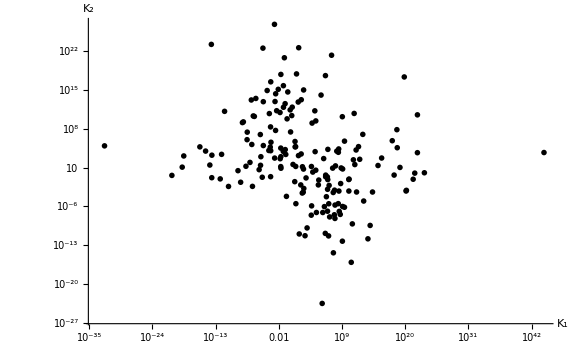

```mathematica
biPlot=ListLogLogPlot[Transpose[{biParK1,biParK2}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->{Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}], Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}]},TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Monochrome"]
```

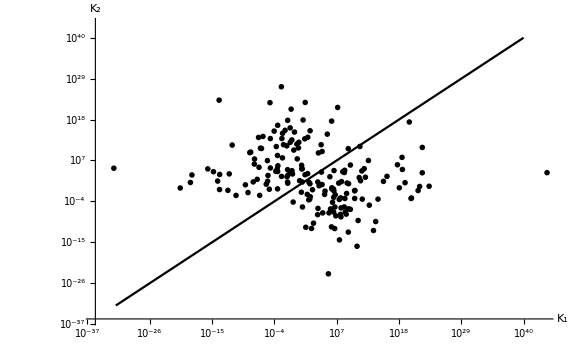

```mathematica
Show[LogLogPlot[x,{x,10^(-32),10^40},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->{Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}], Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}]},TicksStyle->Directive["Label", 14],AxesStyle-> Thick],biPlot]
```

```mathematica
Length[bistableKs]
```

1626

```mathematica
transposedKs=Transpose[bistableKs];parK1=(transposedKs[[1]]*transposedKs[[10]])/(transposedKs[[2]]*transposedKs[[11]]);parK2=(transposedKs[[4]]*transposedKs[[8]])/(transposedKs[[5]]*transposedKs[[9]]);
```

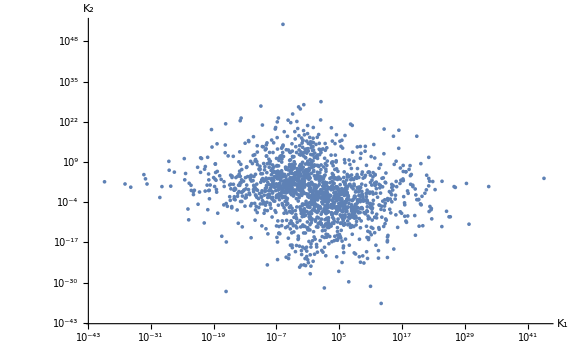

```mathematica
plot=ListLogLogPlot[Transpose[{parK1,parK2}],AxesLabel->{"K_1","K_2"},ImageSize->Large,PlotRange->Full,LabelStyle->{32,GrayLevel[0]},AxesStyle-> Thick,Ticks->Automatic,TicksStyle->Directive["Label", 20]]
```

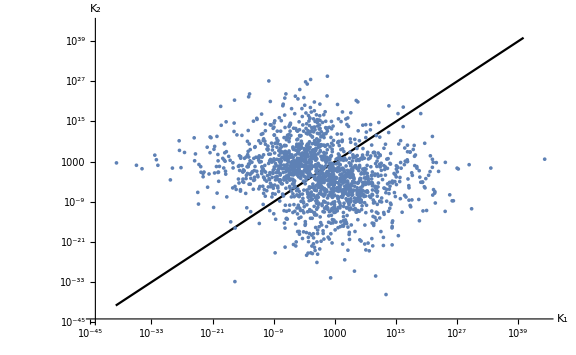

```mathematica
Show[LogLogPlot[x,{x,10^(-40),10^40},PlotRange->Full,ImageSize->Large,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->Automatic(*{Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}], Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}]}*),TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Monochrome"],plot]
```

## Sampling the parameters (with thermodynamic constraint)

Here we try to sampling the parameters by enforcing the thermodynamc constraint. The parameters are sampled in biologically meaningful ranges.

Sampling the parameters related to thermodynamic constraint k1, k2, k4, k5, k8, k9, k10, k11. Using Gamma distribution with α = 7, β = 2, and then uniformly sample 4 random numbers that sum to 1, these are for k1, k5, k9, k10. Sample anther four uniform random number for k2, k4, k8, k11.

For other parameters:

```mathematica
ClearAll["Global`*"];
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms];
(*The above code is the same as first section*)


bistableKs={};
bistableParSets={};
SeedRandom[];
Timing[
Do[{
gamma=RandomVariate[GammaDistribution[2,7]];
rand13=RandomVariate[DirichletDistribution[{1,1,1,1}]];
rand11=1-Total@rand13;
rand23=RandomVariate[DirichletDistribution[{1,1,1,1}]];
rand21=1-Total@rand23;
k1=Exp[-gamma*rand13[[1]]]*1.*^3;k2=Exp[-gamma*rand23[[3]]]*1.*^3;k3=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])]]]*1000;k4=Exp[-gamma*rand23[[1]]]*1.*^3;k5=Exp[-gamma*rand13[[3]]]*1.*^3;k6=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])]]]*1000;k7=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])]]]*1000;
k8=Exp[-gamma*rand23[[2]]]*1.*^3;
k9=Exp[-gamma*rand11]*1.*^3;
k10=Exp[-gamma*rand13[[2]]]*1.*^3;
k11=Exp[-gamma*rand21]*1.*^3;
left=(k3-k6) (((k5+k6) k9 k10)/k4-((k2+k3) k8 k11)/k1);right=(((k5+k6) k10)/k4+((k2+k3) k11)/k1) (k6 k10+k3 k11+k7 (k10+k11));If[left>right,{
AppendTo[bistableKs,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,left,right}];
counter=1;hitQ=0;
While[hitQ==0&&counter≤1000,{
x1=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.0001])]]]*1000;
finalSol=NSolve[finalSubs==0/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1},{Subscript[x, 3]}];
x3=Subscript[x, 3]/.finalSol[[1]];
realSol=solution/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1,Subscript[x, 3]->x3};
T1=(Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
T2=(Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
If[0.0001≤T1≤1000&&0.0001≤T2≤1000,{
AppendTo[bistableParSets,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,T1,T2,left,right}];
hitQ=1;
}];
counter++;
}];
}];
},{i,10000}];
]
```

{968.207,Null}

```mathematica
Length[bistableParSets]
```

10

```mathematica
InputForm[bistableParSets]
```

{{79.96925401169008, 0.029162755292384164, 0.1140572889623974, 339.9710565197557, 233.82687444622428, 114.64226064732323, 
  0.0026653378838017924, 848.0814624988211, 98.0763198422986, 0.12619325577159665, 27.523883235818637, 75.53549893278465, 
  0.21784454128365366, 3334.951424572326, 3.1583906774386863}, {7.0407389028226355, 0.0008224097291961956, 
  0.022012926151557918, 401.15438043780716, 25.357045093495817, 406.19014937715247, 2.927917634249969*^-7, 53.67001503191643, 
  20.559244834670906, 0.21704069940157816, 44.99183701772713, 862.318382770165, 0.00012462837984111196, 1231.2623091299015, 
  33.824226747395265}, {305.1991093062434, 784.3737124091133, 619.82637855117, 50.916812078238046, 0.03989183471052562, 
  103.1422207651505, 0.00009615735390542761, 9.355029822594844, 223.8514742126822, 160.91744917205872, 1.173818527621572, 
  199.7173004058969, 0.00011587014463072953, 3.7690401551549785*^7, 5.743178555595361*^6}, 
 {36.81864149905964, 659.041896529781, 96.5118740002914, 35.82392226394757, 0.005916307051955407, 0.02651008271365682, 
  1.7108210874551764, 0.26414718929071834, 267.16821436188894, 0.26444478905548685, 0.0024677781524620876, 342.1959592859127, 
  144.0991423332005, 4.879648082213135, 0.0357089768834993}, {32.149478677994004, 256.19578446179867, 15.120614031994569, 
  48.533459200047446, 0.00020842276281625365, 0.006943163800317498, 0.0003830525246081422, 0.23330231389801262, 
  267.0058657606572, 4.499352192086573, 0.0027749655960244007, 18.43824828699346, 0.19389924943932862, 2.5929061840151646, 
  0.0018042719455556141}, {149.89233556195757, 95.12174637165315, 69.3654470782759, 291.54913772280514, 0.15791639256623458, 
  2.519161939397978, 0.00013093024641385833, 0.7911846442410612, 18.160496573316713, 3.017103140030287, 0.05910920135334765, 
  10.01342676756553, 0.00021131381998175917, 30.200820078745593, 1.0831531801853953}, 
 {20.127872532643252, 0.0003133225443978319, 30.74274557763445, 493.62928939657775, 134.65295247319492, 105.8207081208534, 
  0.000017784752489717836, 267.0791729419947, 84.44730358642785, 0.01936476924412682, 107.29494937235063, 269.76116399244177, 
  0.00012110711056150803, 3.286041766641667*^6, 540935.372451751}, {168.27980540288368, 0.02776793795941468, 32.33254696253153, 
  659.5321083666223, 37.06870237804975, 280.1944486830178, 34.705991369127666, 303.7385254523473, 11.082870168231395, 
  12.30372914830827, 152.91459483003842, 270.0539849225215, 99.98676017351923, 2.197546272637135*^6, 498976.1775515157}, 
 {345.49429827326423, 0.05247863362064721, 0.38809790650294373, 191.03720181629416, 314.80045197093773, 63.96951070080374, 
  0.022644355878415345, 103.25951825834322, 1.891799857799716, 0.33653343852317413, 66.88813416343318, 653.5971445751168, 
  19.74058395159674, 479.7438053589221, 36.8815398730932}, {66.4018838052063, 0.002850703230181858, 593.7791294404261, 
  208.46562662075124, 1.3580023088499898*^-9, 94.86939488594105, 61.51216015207017, 0.0007788217159391576, 964.8914981387458, 
  48.578349561777564, 9.13224655803779, 786.9979175109088, 166.91082732711357, 1.0642253345824046*^7, 1.4093048791751107*^6}}

```mathematica
transposedBiKs=Transpose[bistableParSets];biParK1=(transposedBiKs[[1]]*transposedBiKs[[10]])/(transposedBiKs[[2]]*transposedBiKs[[11]]);biParK2=(transposedBiKs[[4]]*transposedBiKs[[8]])/(transposedBiKs[[5]]*transposedBiKs[[9]]);
```

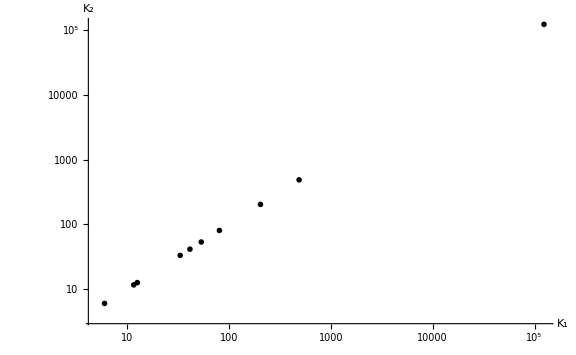

```mathematica
biPlot=ListLogLogPlot[Transpose[{biParK1,biParK2}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Monochrome"]
```

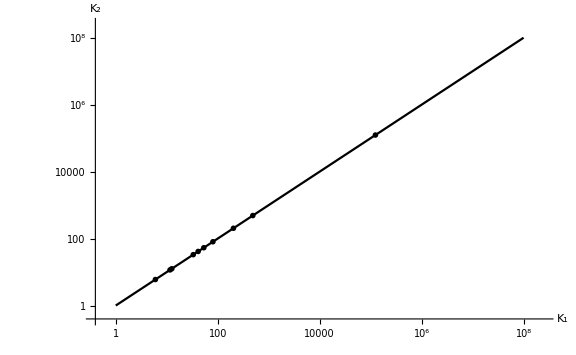

```mathematica
Show[LogLogPlot[x,{x,10^(0),10^8},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick],biPlot]
```

```mathematica
Length[bistableKs]
```

164

```mathematica
transposedKs=Transpose[bistableKs];parK1=(transposedKs[[1]]*transposedKs[[10]])/(transposedKs[[2]]*transposedKs[[11]]);parK2=(transposedKs[[4]]*transposedKs[[8]])/(transposedKs[[5]]*transposedKs[[9]]);
```

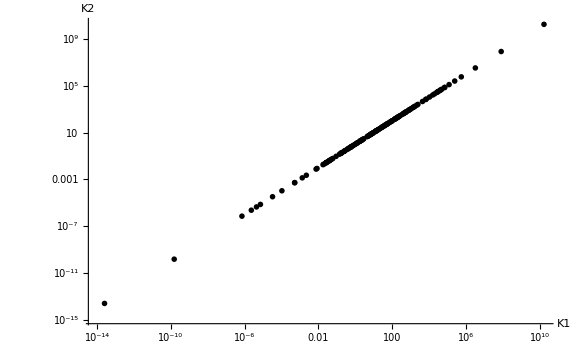

```mathematica
plot=ListLogLogPlot[Transpose[{parK1,parK2}],AxesLabel->{"K1","K2"},ImageSize->Large,PlotRange->Full,LabelStyle->{32,GrayLevel[0]},AxesStyle-> Thick,Ticks->Automatic,TicksStyle->Directive["Label", 20], PlotTheme->"Monochrome"]
```

These above results show that the parameter set within biological meaningful ranges can be reached by increasing the sampling size even when enforcing the thermodynamic constraint. Comparing to results from the other document (without enforcing thermodynamic constraint), the paramter space is largely reduced. 

Conditions | with thermo | with thermo | without thermo | without thermo
Sampling size | only check 
bistability | bistability &
 concentrations | only check 
bistability | bistability & 
concentrations
10^4 | 164 | 10 | 1626 | 185
10^5 | 1924 | N/A | 14502 | N/A

#### From the sampling results, thermodynamic constraint indeed shrinks the parameter space for bistability in the motif. Although, the concentration is probably not very well sampled, the concentration is trivial for its purpose here.

## Test

```mathematica
Exp[-RandomVariate[ExponentialDistribution[1/(-Log[0.01])],10]]*10
```

{7.85861,4.74129,0.00193437,3.56052,0.0092094,0.389896,0.000290741,0.194143,0.000170171,0.953613}

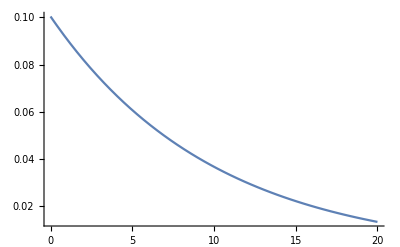

```mathematica
Plot[PDF[ExponentialDistribution[Log[2]/(-Log[0.001])],x],{x,0,20},PlotRange->Full]
```

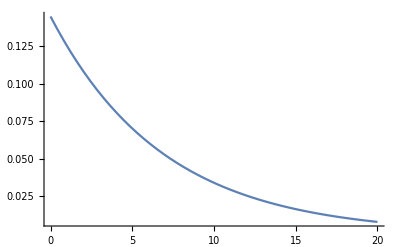

```mathematica
Plot[PDF[ExponentialDistribution[1/(-Log[0.001])],x],{x,0,20},PlotRange->Full]
```

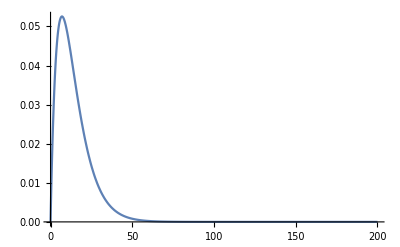

```mathematica
Plot[PDF[GammaDistribution[2,7],x],{x,0,200},PlotRange->Full]
```

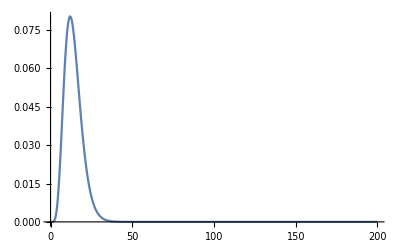

```mathematica
Plot[PDF[GammaDistribution[7,2],x],{x,0,200},PlotRange->Full]
```

```mathematica
PDF[GammaDistribution[7,1],x]
```

Piecewise[{{1/720 ⅇ^-x x^6, x>0}, {0, True}}]

```mathematica
1/720 ⅇ^-x x^6
```

```mathematica
-Log[0.001]
```

6.90776

```mathematica
Log[0.001]
```

-6.90776